# PME-3380: Projeto Semestral

## Modelagem da estabilidade de um helicóptero extintor

## Equações de Lagrange

### Posições dos centros de massa:

-Graphics-

Ponto P -> Ponto referente à articulação.

```mathematica
xP[t]=x1[t]+L1 Sin[θ1[t]];
yP[t]=y1[t]-L1 Cos[θ1[t]];
x2[t]=xP[t]+L2 Sin[θ2[t]];
y2[t]=yP[t]-L2 Cos[θ2[t]];
x1'[t]=D[x1[t],t];
y1'[t]=D[y1[t],t];
x2'[t]=D[x2[t],t];
y2'[t]=D[y2[t],t];
v1[t]=Simplify[Sqrt[x1'[t]^2+y1'[t]^2]];
v2[t]=Simplify[Sqrt[x2'[t]^2+y2'[t]^2]];
vfa1[t]=x1'[t];
vfa2[t]=x2'[t];
vfb1[t]=y1'[t];
vfb2[t]=y2'[t];
```

### Energia Cinética:

```mathematica
T1=Simplify[1/2 m1 v1[t]^2+1/2 IG1(θ1'[t])^2];
T2=Simplify[1/2 m2 v2[t]^2+1/2 IG2(θ2'[t])^2];
T=T1+T2;
TraditionalForm[T]
```

1/2 (IG1 (θ1'(t))^2+m1 (x1'(t))^2+m1 (y1'(t))^2)+1/2 (IG2 (θ2'(t))^2+m2 ((L1 θ1'(t) cos(θ1(t))+L2 θ2'(t) cos(θ2(t))+x1'(t))^2+(L1 θ1'(t) sin(θ1(t))+L2 θ2'(t) sin(θ2(t))+y1'(t))^2))

### Energia Potencial:

```mathematica
V1=Simplify[m1 g y1[t]];
V2=Simplify[m2 g y2[t]];
V=V1+V2;
TraditionalForm[V]
```

g m2 (-L1 cos(θ1(t))-L2 cos(θ2(t))+y1(t))+g m1 y1(t)

### Função de Lagrange:

```mathematica
L=Simplify[T-V];
TraditionalForm[L]
```

1/2 (2 g m2 (L1 cos(θ1(t))+L2 cos(θ2(t))-y1(t))-2 g m1 y1(t)+IG1 (θ1'(t))^2+IG2 (θ2'(t))^2+m2 ((L1 θ1'(t) cos(θ1(t))+L2 θ2'(t) cos(θ2(t))+x1'(t))^2+(L1 θ1'(t) sin(θ1(t))+L2 θ2'(t) sin(θ2(t))+y1'(t))^2)+m1 (x1'(t))^2+m1 (y1'(t))^2)

### Função Dissipativa de Rayleigh:

```mathematica
R=1/2 c (θ1'[t]-θ2'[t])^2;
TraditionalForm[R]
```

1/2 c (θ1'(t)-θ2'(t))^2

### Forças Generalizadas por Trabalhos Virtuais:

```mathematica
Fx1=FA1[t]+FH[t];
Fy1=FB1[t]+FS[t];
Fx2=FA2[t];
Fy2=FB2[t];
Qx1=Fx1 D[x1[t], x1[t]]+Fx2 D[x2[t], x1[t]]+Fy1 D[y1[t], x1[t]]+Fy2 D[y2[t], x1[t]];
Qθ1=Fx1 D[x1[t], θ1[t]]+Fx2 D[x2[t], θ1[t]]+Fy1 D[y1[t], θ1[t]]+Fy2 D[y2[t], θ1[t]]+MG[t];
Qθ2=Fx1 D[x1[t], θ2[t]]+Fx2 D[x2[t], θ2[t]]+Fy1 D[y1[t], θ2[t]]+Fy2 D[y2[t], θ2[t]];
Qy1=Fx1 D[x1[t], y1[t]]+Fx2 D[x2[t], y1[t]]+Fy1 D[y1[t], y1[t]]+Fy2 D[y2[t], y1[t]];
TraditionalForm[({{Qx1}, {Qθ1}, {Qθ2}, {Qy1}})]
```

(FA1(t)+FA2(t)+FH(t)
L1 FA2(t) cos(θ1(t))+L1 FB2(t) sin(θ1(t))+MG(t)
L2 FA2(t) cos(θ2(t))+L2 FB2(t) sin(θ2(t))
FB1(t)+FB2(t)+FS(t))

### Euler-Lagrange com dissipação:

```mathematica
SubRes={FA1[t]->-1/2 Subscript[C, 1] ρ Subscript[Α, 1] vfa1[t]*RealAbs[vfa1[t]],FA2[t]->-1/2 Subscript[C, 2] ρ Subscript[Α, 2] vfa2[t]*RealAbs[vfa2[t]],FB1[t]->-1/2 Subscript[C, 3] ρ Subscript[Α, 3] vfb1[t]*RealAbs[vfb1[t]],FB2[t]->-1/2 Subscript[C, 4] ρ Subscript[Α, 4] vfb2[t]*RealAbs[vfb2[t]]};
EL1=D[D[L, x1'[t]],t]-D[L, x1[t]]+D[R, x1'[t]]//TrigReduce//FullSimplify;
EL2=D[D[L, θ1'[t]],t]-D[L, θ1[t]]+D[R, θ1'[t]]//TrigReduce//FullSimplify;
EL3=D[D[L, θ2'[t]],t]-D[L, θ2[t]]+D[R, θ2'[t]]//TrigReduce//FullSimplify;
EL4=D[D[L, y1'[t]],t]-D[L, y1[t]]+D[R, y1'[t]]//TrigReduce//FullSimplify;
EL={EL1==Qx1/.SubRes,EL2==Qθ1/.SubRes,EL3==Qθ2/.SubRes,EL4==Qy1/.SubRes};
Simplify[TraditionalForm[TableForm[EL]]]
```

1/2 ρ (Α_2 C_2 (L1 θ1'(t) cos(θ1(t))+L2 θ2'(t) cos(θ2(t))+x1'(t)) x1'(t)+L1 cos(θ1(t)) θ1'(t)+L2 cos(θ2(t)) θ2'(t)+Α_1 C_1 x1'(t) x1'(t))+m2 (L1 θ1''(t) cos(θ1(t))-L1 (θ1'(t))^2 sin(θ1(t))+L2 θ2''(t) cos(θ2(t))-L2 (θ2'(t))^2 sin(θ2(t))+x1''(t))+m1 x1''(t)==FH(t)
c θ1'(t)+1/2 Α_2 C_2 L1 ρ cos(θ1(t)) (L1 θ1'(t) cos(θ1(t))+L2 θ2'(t) cos(θ2(t))+x1'(t)) x1'(t)+L1 cos(θ1(t)) θ1'(t)+L2 cos(θ2(t)) θ2'(t)+1/2 Α_4 C_4 L1 ρ sin(θ1(t)) (L1 θ1'(t) sin(θ1(t))+L2 θ2'(t) sin(θ2(t))+y1'(t)) y1'(t)+L1 sin(θ1(t)) θ1'(t)+L2 sin(θ2(t)) θ2'(t)+g L1 m2 sin(θ1(t))+IG1 θ1''(t)+L1 L2 m2 (θ2'(t))^2 sin(θ1(t)-θ2(t))+L1 m2 (L1 θ1''(t)+L2 θ2''(t) cos(θ1(t)-θ2(t))+cos(θ1(t)) x1''(t)+sin(θ1(t)) y1''(t))==c θ2'(t)+MG(t)
c θ2'(t)+1/2 L2 ρ (Α_2 C_2 cos(θ2(t)) (L1 θ1'(t) cos(θ1(t))+L2 θ2'(t) cos(θ2(t))+x1'(t)) x1'(t)+L1 cos(θ1(t)) θ1'(t)+L2 cos(θ2(t)) θ2'(t)+Α_4 C_4 sin(θ2(t)) (L1 θ1'(t) sin(θ1(t))+L2 θ2'(t) sin(θ2(t))+y1'(t)) y1'(t)+L1 sin(θ1(t)) θ1'(t)+L2 sin(θ2(t)) θ2'(t))+L2 m2 (sin(θ2(t)) (g+y1''(t))+L1 θ1''(t) cos(θ1(t)-θ2(t))+cos(θ2(t)) x1''(t))+(IG2+L2^2 m2) θ2''(t)==θ1'(t) (c+L1 L2 m2 θ1'(t) sin(θ1(t)-θ2(t)))
1/2 ρ (Α_4 C_4 (L1 θ1'(t) sin(θ1(t))+L2 θ2'(t) sin(θ2(t))+y1'(t)) y1'(t)+L1 sin(θ1(t)) θ1'(t)+L2 sin(θ2(t)) θ2'(t)+Α_3 C_3 y1'(t) y1'(t))+g (m1+m2)+m2 (L1 θ1''(t) sin(θ1(t))+L1 (θ1'(t))^2 cos(θ1(t))+L2 θ2''(t) sin(θ2(t))+L2 (θ2'(t))^2 cos(θ2(t))+y1''(t))+m1 y1''(t)==FS(t)

## Espaço de Estados Não-Linear

### Substituindo as Variáveis de Estado e Isolando Derivadas:

```mathematica
Subs1={θ1[t]->Subscript[x, 1][t],θ2[t]->Subscript[x, 2][t],x1'[t]->Subscript[x, 3][t],
y1'[t]->Subscript[x, 4][t],θ1'[t]->Subscript[x, 5][t],θ2'[t]->Subscript[x, 6][t]};
ELnl=EL/.Subs1;
PPnl=Solve[ELnl,{x1''[t],y1''[t],θ1''[t],θ2''[t]}]//First;
```

### Apresentação Literal:

```mathematica
𝕩[t]={Subscript[x, 1][t],Subscript[x, 2][t],Subscript[x, 3][t],Subscript[x, 4][t],Subscript[x, 5][t],Subscript[x, 6][t]};
𝕩'[t]={Subscript[x, 5][t],Subscript[x, 6][t],x1''[t],y1''[t],θ1''[t],θ2''[t]};
EENL={D[𝕩[t],t]==𝕩'[t]/.PPnl[[1]]/.PPnl[[2]]/.PPnl[[3]]/.PPnl[[4]],{θ1[t],θ2[t],x1'[t]}=={Subscript[x, 1][t],Subscript[x, 2][t],Subscript[x, 3][t]}};
TraditionalForm[TableForm[EENL]]
```

{x_1'(t),x_2'(t),x_3'(t),x_4'(t),x_5'(t),x_6'(t)}=={x_5(t),x_6(t),-((L2 m2 cos(x_2(t)) (L1^2 L2 m2^2 cos(x_1(t)-x_2(t)) sin(x_1(t))-L2 m2 (m2 L1^2+IG1) sin(x_2(t)))-L1 m2 cos(x_1(t)) (L1 m2 (m2 L2^2+IG2) sin(x_1(t))-L1 L2^2 m2^2 cos(x_1(t)-x_2(t)) sin(x_2(t)))) (L2 m2 cos(x_2(t)) (L1 m2 sin(x_1(t)) (L1 m2 cos(x_1(t)) (x_5(t))^2+L2 m2 cos(x_2(t)) (x_6(t))^2+g (m1+m2)-FS(t)+1/2 ρ x_4(t) C_3 Α_3 x_4(t)+1/2 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) C_4 Α_4 (x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t)))-(m1+m2) (L1 L2 m2 sin(x_1(t)-x_2(t)) (x_6(t))^2-c x_6(t)-MG(t)+g L1 m2 sin(x_1(t))+c x_5(t)+1/2 L1 ρ cos(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) C_2 Α_2 (x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t))+1/2 L1 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sin(x_1(t)) C_4 Α_4 (x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t))))-(L1 L2 m2^2 sin(x_1(t)) sin(x_2(t))-L1 L2 m2 (m1+m2) cos(x_1(t)-x_2(t))) (-L1 m2 sin(x_1(t)) (x_5(t))^2-L2 m2 sin(x_2(t)) (x_6(t))^2-FH(t)+1/2 ρ x_3(t) C_1 Α_1 x_3(t)+1/2 ρ x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) C_2 Α_2 (x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t))))-(L2 m2 cos(x_2(t)) (L1^2 m2^2 sin^2(x_1(t))-(m1+m2) (m2 L1^2+IG1))-L1 m2 cos(x_1(t)) (L1 L2 m2^2 sin(x_1(t)) sin(x_2(t))-L1 L2 m2 (m1+m2) cos(x_1(t)-x_2(t)))) (L2 m2 cos(x_2(t)) (L1 m2 sin(x_1(t)) (-L1 L2 m2 sin(x_1(t)-x_2(t)) (x_5(t))^2-c x_5(t)+g L2 m2 sin(x_2(t))+c x_6(t)+1/2 L2 ρ cos(x_2(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) C_2 Α_2 (x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t))+1/2 L2 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sin(x_2(t)) C_4 Α_4 (x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t)))-L2 m2 sin(x_2(t)) (L1 L2 m2 sin(x_1(t)-x_2(t)) (x_6(t))^2-c x_6(t)-MG(t)+g L1 m2 sin(x_1(t))+c x_5(t)+1/2 L1 ρ cos(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) C_2 Α_2 (x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t))+1/2 L1 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sin(x_1(t)) C_4 Α_4 (x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t))))-(L1 m2 (m2 L2^2+IG2) sin(x_1(t))-L1 L2^2 m2^2 cos(x_1(t)-x_2(t)) sin(x_2(t))) (-L1 m2 sin(x_1(t)) (x_5(t))^2-L2 m2 sin(x_2(t)) (x_6(t))^2-FH(t)+1/2 ρ x_3(t) C_1 Α_1 x_3(t)+1/2 ρ x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) C_2 Α_2 (x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t)))))/((L2 m2 cos(x_2(t)) (L1^2 L2 m2^2 cos(x_1(t)-x_2(t)) sin(x_1(t))-L2 m2 (m2 L1^2+IG1) sin(x_2(t)))-L1 m2 cos(x_1(t)) (L1 m2 (m2 L2^2+IG2) sin(x_1(t))-L1 L2^2 m2^2 cos(x_1(t)-x_2(t)) sin(x_2(t)))) (-L1 L2 (m1+m2) cos(x_1(t)) cos(x_2(t)) m2^2-(m1+m2) (L1 L2 m2^2 sin(x_1(t)) sin(x_2(t))-L1 L2 m2 (m1+m2) cos(x_1(t)-x_2(t))))-(L2 m2 cos(x_2(t)) (L1 L2 m2^2 cos(x_2(t)) sin(x_1(t))-L1 L2 m2^2 cos(x_1(t)) sin(x_2(t)))-(m1+m2) (L1 m2 (m2 L2^2+IG2) sin(x_1(t))-L1 L2^2 m2^2 cos(x_1(t)-x_2(t)) sin(x_2(t)))) (L2 m2 cos(x_2(t)) (L1^2 m2^2 sin^2(x_1(t))-(m1+m2) (m2 L1^2+IG1))-L1 m2 cos(x_1(t)) (L1 L2 m2^2 sin(x_1(t)) sin(x_2(t))-L1 L2 m2 (m1+m2) cos(x_1(t)-x_2(t))))),-(cos(x_2(t)) sin(x_1(t)) (-2 g L1^2 L2^2 csc^3(x_1(t)) sec^3(x_2(t)) m2^4+2 g L1^2 L2^2 cos^2(x_1(t)-x_2(t)) csc^3(x_1(t)) sec^3(x_2(t)) m2^4+2 g L1^2 L2^2 csc(x_1(t)) sec^3(x_2(t)) m2^4+2 g L1^2 L2^2 cot^2(x_1(t)) csc(x_1(t)) sec^3(x_2(t)) m2^4-4 g L1^2 L2^2 cos(x_1(t)-x_2(t)) cot(x_1(t)) csc^2(x_1(t)) sec^2(x_2(t)) m2^4+2 g L1^2 L2^2 csc^3(x_1(t)) sec(x_2(t)) tan^2(x_2(t)) m2^4-2 g L1^2 L2^2 cot^2(x_1(t)) csc(x_1(t)) sec(x_2(t)) tan^2(x_2(t)) m2^4+2 L1^3 L2^2 cot^3(x_1(t)) sec^3(x_2(t)) (x_5(t))^2 m2^4-2 L1^3 L2^2 cot(x_1(t)) csc^2(x_1(t)) sec^3(x_2(t)) (x_5(t))^2 m2^4+2 L1^3 L2^2 cos^2(x_1(t)-x_2(t)) cot(x_1(t)) csc^2(x_1(t)) sec^3(x_2(t)) (x_5(t))^2 m2^4+2 L1^3 L2^2 cot(x_1(t)) sec^3(x_2(t)) (x_5(t))^2 m2^4-4 L1^3 L2^2 cos(x_1(t)-x_2(t)) cot^2(x_1(t)) csc(x_1(t)) sec^2(x_2(t)) (x_5(t))^2 m2^4-2 L1^3 L2^2 cos(x_1(t)-x_2(t)) csc(x_1(t)) sec^2(x_2(t)) (x_5(t))^2 m2^4+2 L1^3 L2^2 cot(x_1(t)) csc^2(x_1(t)) sec(x_2(t)) (x_5(t))^2 m2^4+2 L1^3 L2^2 cos(x_1(t)-x_2(t)) csc^2(x_1(t)) sec^3(x_2(t)) sin(x_1(t)-x_2(t)) (x_5(t))^2 m2^4-2 L1^3 L2^2 cot(x_1(t)) csc(x_1(t)) sec^2(x_2(t)) sin(x_1(t)-x_2(t)) (x_5(t))^2 m2^4-2 L1^3 L2^2 cos(x_1(t)-x_2(t)) cot(x_1(t)) csc(x_1(t)) sec^2(x_2(t)) tan(x_2(t)) (x_5(t))^2 m2^4+2 L1^3 L2^2 csc^2(x_1(t)) sec(x_2(t)) tan(x_2(t)) (x_5(t))^2 m2^4-2 L1^3 L2^2 csc^3(x_1(t)) sec^2(x_2(t)) sin(x_1(t)-x_2(t)) tan(x_2(t)) (x_5(t))^2 m2^4+2 L1^3 L2^2 cot^2(x_1(t)) csc(x_1(t)) sec^2(x_2(t)) sin(x_1(t)-x_2(t)) tan(x_2(t)) (x_5(t))^2 m2^4+2 L1^2 L2^3 csc^3(x_1(t)) (x_6(t))^2 m2^4-2 L1^2 L2^3 csc^3(x_1(t)) sec^2(x_2(t)) (x_6(t))^2 m2^4+2 L1^2 L2^3 cos^2(x_1(t)-x_2(t)) csc^3(x_1(t)) sec^2(x_2(t)) (x_6(t))^2 m2^4+2 L1^2 L2^3 cot^2(x_1(t)) csc(x_1(t)) sec^2(x_2(t)) (x_6(t))^2 m2^4+2 L1^2 L2^3 csc^3(x_1(t)) tan^2(x_2(t)) (x_6(t))^2 m2^4-2 L1^2 L2^3 cos(x_1(t)-x_2(t)) cot(x_1(t)) csc^2(x_1(t)) sec(x_2(t)) tan^2(x_2(t)) (x_6(t))^2 m2^4-4 L1^2 L2^3 cos(x_1(t)-x_2(t)) cot(x_1(t)) csc^2(x_1(t)) sec(x_2(t)) (x_6(t))^2 m2^4+2 L1^2 L2^3 csc^2(x_1(t)) sec^3(x_2(t)) sin(x_1(t)-x_2(t)) (x_6(t))^2 m2^4-2 L1^2 L2^3 csc^2(x_1(t)) sec(x_2(t)) sin(x_1(t)-x_2(t)) (x_6(t))^2 m2^4+2 L1^2 L2^3 cot(x_1(t)) csc(x_1(t)) sec^2(x_2(t)) tan(x_2(t)) (x_6(t))^2 m2^4-2 L1^2 L2^3 cos(x_1(t)-x_2(t)) csc^2(x_1(t)) sec(x_2(t)) tan(x_2(t)) (x_6(t))^2 m2^4-2 L1^2 L2^3 cos(x_1(t)-x_2(t)) csc^3(x_1(t)) sec^2(x_2(t)) sin(x_1(t)-x_2(t)) tan(x_2(t)) (x_6(t))^2 m2^4+2 L1^2 L2^3 cot(x_1(t)) csc^2(x_1(t)) sec(x_2(t)) sin(x_1(t)-x_2(t)) tan(x_2(t)) (x_6(t))^2 m2^4+2 g L1^2 L2^2 csc^3(x_1(t)) sec(x_2(t)) m2^4-2 g L1^2 L2^2 csc(x_1(t)) sec(x_2(t)) m2^4-4 g L1^2 L2^2 cos(x_1(t)-x_2(t)) csc^2(x_1(t)) sec^2(x_2(t)) tan(x_2(t)) m2^4+4 g L1^2 L2^2 cot(x_1(t)) csc(x_1(t)) sec(x_2(t)) tan(x_2(t)) m2^4-2 g IG2 L1^2 csc^3(x_1(t)) sec^3(x_2(t)) m2^3-2 g IG1 L2^2 csc^3(x_1(t)) sec^3(x_2(t)) m2^3+4 g L1^2 L2^2 m1 cos^2(x_1(t)-x_2(t)) csc^3(x_1(t)) sec^3(x_2(t)) m2^3-4 g L1^2 L2^2 m1 csc^3(x_1(t)) sec^3(x_2(t)) m2^3+2 g IG2 L1^2 csc(x_1(t)) sec^3(x_2(t)) m2^3+2 g IG2 L1^2 cot^2(x_1(t)) csc(x_1(t)) sec^3(x_2(t)) m2^3+2 g L1^2 L2^2 m1 cot^2(x_1(t)) csc(x_1(t)) sec^3(x_2(t)) m2^3+2 g L1^2 L2^2 m1 csc(x_1(t)) sec^3(x_2(t)) m2^3+2 L1^2 L2^2 cot(x_1(t)) csc(x_1(t)) FH(t) sec^3(x_2(t)) m2^3+2 L1^2 L2^2 csc^3(x_1(t)) FS(t) sec^3(x_2(t)) m2^3-2 L1^2 L2^2 cos^2(x_1(t)-x_2(t)) csc^3(x_1(t)) FS(t) sec^3(x_2(t)) m2^3-2 L1^2 L2^2 cot^2(x_1(t)) csc(x_1(t)) FS(t) sec^3(x_2(t)) m2^3-2 L1 L2^2 csc^2(x_1(t)) MG(t) sec^3(x_2(t)) m2^3-4 g L1^2 L2^2 m1 cos(x_1(t)-x_2(t)) cot(x_1(t)) csc^2(x_1(t)) sec^2(x_2(t)) m2^3-2 L1^2 L2^2 cos(x_1(t)-x_2(t)) csc^2(x_1(t)) FH(t) sec^2(x_2(t)) m2^3+4 L1^2 L2^2 cos(x_1(t)-x_2(t)) cot(x_1(t)) csc^2(x_1(t)) FS(t) sec^2(x_2(t)) m2^3+2 g IG1 L2^2 csc^3(x_1(t)) sec(x_2(t)) tan^2(x_2(t)) m2^3+2 g L1^2 L2^2 m1 csc^3(x_1(t)) sec(x_2(t)) tan^2(x_2(t)) m2^3+2 IG2 L1^3 cot^3(x_1(t)) sec^3(x_2(t)) (x_5(t))^2 m2^3-2 IG2 L1^3 cot(x_1(t)) csc^2(x_1(t)) sec^3(x_2(t)) (x_5(t))^2 m2^3-2 IG1 L1 L2^2 cot(x_1(t)) csc^2(x_1(t)) sec^3(x_2(t)) (x_5(t))^2 m2^3+2 L1^3 L2^2 m1 cos^2(x_1(t)-x_2(t)) cot(x_1(t)) csc^2(x_1(t)) sec^3(x_2(t)) (x_5(t))^2 m2^3-2 L1^3 L2^2 m1 cot(x_1(t)) csc^2(x_1(t)) sec^3(x_2(t)) (x_5(t))^2 m2^3+2 IG2 L1^3 cot(x_1(t)) sec^3(x_2(t)) (x_5(t))^2 m2^3+2 IG1 L1 L2^2 cot(x_1(t)) csc^2(x_1(t)) sec(x_2(t)) (x_5(t))^2 m2^3+2 L1^3 L2^2 m1 cos(x_1(t)-x_2(t)) csc^2(x_1(t)) sec^3(x_2(t)) sin(x_1(t)-x_2(t)) (x_5(t))^2 m2^3+2 IG1 L1 L2^2 csc^2(x_1(t)) sec(x_2(t)) tan(x_2(t)) (x_5(t))^2 m2^3-2 IG1 L1 L2^2 csc^3(x_1(t)) sec^2(x_2(t)) sin(x_1(t)-x_2(t)) tan(x_2(t)) (x_5(t))^2 m2^3-2 L1^3 L2^2 m1 csc^3(x_1(t)) sec^2(x_2(t)) sin(x_1(t)-x_2(t)) tan(x_2(t)) (x_5(t))^2 m2^3+2 IG1 L2^3 csc^3(x_1(t)) (x_6(t))^2 m2^3-2 IG1 L2^3 csc^3(x_1(t)) sec^2(x_2(t)) (x_6(t))^2 m2^3+2 L1^2 L2^3 m1 cos^2(x_1(t)-x_2(t)) csc^3(x_1(t)) sec^2(x_2(t)) (x_6(t))^2 m2^3-2 IG2 L1^2 L2 csc^3(x_1(t)) sec^2(x_2(t)) (x_6(t))^2 m2^3-2 L1^2 L2^3 m1 csc^3(x_1(t)) sec^2(x_2(t)) (x_6(t))^2 m2^3+2 IG2 L1^2 L2 cot^2(x_1(t)) csc(x_1(t)) sec^2(x_2(t)) (x_6(t))^2 m2^3+2 IG1 L2^3 csc^3(x_1(t)) tan^2(x_2(t)) (x_6(t))^2 m2^3+2 IG2 L1^2 L2 csc^2(x_1(t)) sec^3(x_2(t)) sin(x_1(t)-x_2(t)) (x_6(t))^2 m2^3+2 L1^2 L2^3 m1 csc^2(x_1(t)) sec^3(x_2(t)) sin(x_1(t)-x_2(t)) (x_6(t))^2 m2^3+2 IG2 L1^2 L2 cot(x_1(t)) csc(x_1(t)) sec^2(x_2(t)) tan(x_2(t)) (x_6(t))^2 m2^3-2 L1^2 L2^3 m1 cos(x_1(t)-x_2(t)) csc^3(x_1(t)) sec^2(x_2(t)) sin(x_1(t)-x_2(t)) tan(x_2(t)) (x_6(t))^2 m2^3+2 g IG1 L2^2 csc^3(x_1(t)) sec(x_2(t)) m2^3+2 g L1^2 L2^2 m1 csc^3(x_1(t)) sec(x_2(t)) m2^3-2 L1^2 L2^2 csc^3(x_1(t)) FS(t) sec(x_2(t)) m2^3+2 L1 L2^2 csc^2(x_1(t)) MG(t) sec(x_2(t)) m2^3-4 g L1^2 L2^2 m1 cos(x_1(t)-x_2(t)) csc^2(x_1(t)) sec^2(x_2(t)) tan(x_2(t)) m2^3-2 L1^2 L2^2 cos(x_1(t)-x_2(t)) cot(x_1(t)) csc^2(x_1(t)) FH(t) sec^2(x_2(t)) tan(x_2(t)) m2^3+2 L1 L2^2 cos(x_1(t)-x_2(t)) csc^3(x_1(t)) MG(t) sec^2(x_2(t)) tan(x_2(t)) m2^3+2 L1^2 L2^2 csc^3(x_1(t)) FH(t) sec(x_2(t)) tan(x_2(t)) m2^3-2 L1 L2^2 cot(x_1(t)) csc^2(x_1(t)) MG(t) sec(x_2(t)) tan(x_2(t)) m2^3-L1^2 L2^2 ρ cot(x_1(t)) csc(x_1(t)) x_3(t) sec^3(x_2(t)) C_1 Α_1 x_3(t) m2^3+L1^2 L2^2 ρ cos(x_1(t)-x_2(t)) csc^2(x_1(t)) x_3(t) sec^2(x_2(t)) C_1 Α_1 x_3(t) m2^3+L1^2 L2^2 ρ cos(x_1(t)-x_2(t)) cot(x_1(t)) csc^2(x_1(t)) x_3(t) sec^2(x_2(t)) C_1 Α_1 tan(x_2(t)) x_3(t) m2^3-L1^2 L2^2 ρ csc^3(x_1(t)) x_3(t) sec(x_2(t)) C_1 Α_1 tan(x_2(t)) x_3(t) m2^3+L1^2 L2^2 ρ csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) C_4 Α_4 tan^2(x_2(t)) x_4(t) m2^3-L1^2 L2^2 ρ cot^2(x_1(t)) csc(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) C_4 Α_4 tan^2(x_2(t)) x_4(t) m2^3+L1^2 L2^2 ρ cos^2(x_1(t)-x_2(t)) csc^3(x_1(t)) x_4(t) sec^3(x_2(t)) C_3 Α_3 x_4(t) m2^3-L1^2 L2^2 ρ csc^3(x_1(t)) x_4(t) sec^3(x_2(t)) C_3 Α_3 x_4(t) m2^3+L1^2 L2^2 ρ cot^2(x_1(t)) csc(x_1(t)) x_4(t) sec^3(x_2(t)) C_3 Α_3 x_4(t) m2^3-2 L1^2 L2^2 ρ cos(x_1(t)-x_2(t)) cot(x_1(t)) csc^2(x_1(t)) x_4(t) sec^2(x_2(t)) C_3 Α_3 x_4(t) m2^3+L1^2 L2^2 ρ csc^3(x_1(t)) x_4(t) sec(x_2(t)) C_3 Α_3 x_4(t) m2^3+L1^2 L2^2 ρ cos^2(x_1(t)-x_2(t)) csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_4(t) m2^3-L1^2 L2^2 ρ csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_4(t) m2^3+L1^2 L2^2 ρ cot^2(x_1(t)) csc(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_4(t) m2^3+L1^2 L2^2 ρ csc(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_4(t) m2^3-2 L1^2 L2^2 ρ cos(x_1(t)-x_2(t)) cot(x_1(t)) csc^2(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^2(x_2(t)) C_4 Α_4 x_4(t) m2^3+L1^2 L2^2 ρ csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) C_4 Α_4 x_4(t) m2^3-L1^2 L2^2 ρ csc(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) C_4 Α_4 x_4(t) m2^3-2 L1^2 L2^2 ρ cos(x_1(t)-x_2(t)) csc^2(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^2(x_2(t)) C_4 Α_4 tan(x_2(t)) x_4(t) m2^3+2 L1^2 L2^2 ρ cot(x_1(t)) csc(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) C_4 Α_4 tan(x_2(t)) x_4(t) m2^3+2 c L1 L2^2 csc^2(x_1(t)) sec^3(x_2(t)) x_5(t) m2^3+2 c L1^2 L2 cos(x_1(t)-x_2(t)) csc^2(x_1(t)) sec^3(x_2(t)) x_5(t) m2^3-2 c L1^2 L2 cot(x_1(t)) csc(x_1(t)) sec^2(x_2(t)) x_5(t) m2^3-L1^3 L2^2 ρ cot^2(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) C_4 Α_4 tan^2(x_2(t)) x_5(t) m2^3+L1^3 L2^2 ρ csc^2(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) C_4 Α_4 tan^2(x_2(t)) x_5(t) m2^3-2 c L1 L2^2 csc^2(x_1(t)) sec(x_2(t)) x_5(t) m2^3+L1^3 L2^2 ρ cot^2(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_5(t) m2^3+L1^3 L2^2 ρ cos^2(x_1(t)-x_2(t)) csc^2(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_5(t) m2^3-L1^3 L2^2 ρ csc^2(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_5(t) m2^3+L1^3 L2^2 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_5(t) m2^3-2 L1^3 L2^2 ρ cos(x_1(t)-x_2(t)) cot(x_1(t)) csc(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^2(x_2(t)) C_4 Α_4 x_5(t) m2^3+L1^3 L2^2 ρ csc^2(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) C_4 Α_4 x_5(t) m2^3-L1^3 L2^2 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) C_4 Α_4 x_5(t) m2^3-2 c L1^2 L2 csc^3(x_1(t)) sec^2(x_2(t)) tan(x_2(t)) x_5(t) m2^3-2 c L1 L2^2 cos(x_1(t)-x_2(t)) csc^3(x_1(t)) sec^2(x_2(t)) tan(x_2(t)) x_5(t) m2^3+2 c L1^2 L2 cot^2(x_1(t)) csc(x_1(t)) sec^2(x_2(t)) tan(x_2(t)) x_5(t) m2^3+2 c L1 L2^2 cot(x_1(t)) csc^2(x_1(t)) sec(x_2(t)) tan(x_2(t)) x_5(t) m2^3-2 L1^3 L2^2 ρ cos(x_1(t)-x_2(t)) csc(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^2(x_2(t)) C_4 Α_4 tan(x_2(t)) x_5(t) m2^3+2 L1^3 L2^2 ρ cot(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) C_4 Α_4 tan(x_2(t)) x_5(t) m2^3-2 c L1 L2^2 csc^2(x_1(t)) sec^3(x_2(t)) x_6(t) m2^3-2 c L1^2 L2 cos(x_1(t)-x_2(t)) csc^2(x_1(t)) sec^3(x_2(t)) x_6(t) m2^3+L1^2 L2^3 ρ csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) C_4 Α_4 tan^3(x_2(t)) x_6(t) m2^3-L1^2 L2^3 ρ cot^2(x_1(t)) csc(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) C_4 Α_4 tan^3(x_2(t)) x_6(t) m2^3+2 c L1^2 L2 cot(x_1(t)) csc(x_1(t)) sec^2(x_2(t)) x_6(t) m2^3+2 L1^2 L2^3 ρ cot(x_1(t)) csc(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) C_4 Α_4 tan^2(x_2(t)) x_6(t) m2^3-2 L1^2 L2^3 ρ cos(x_1(t)-x_2(t)) csc^2(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) C_4 Α_4 tan^2(x_2(t)) x_6(t) m2^3+2 c L1 L2^2 csc^2(x_1(t)) sec(x_2(t)) x_6(t) m2^3+2 c L1^2 L2 csc^3(x_1(t)) sec^2(x_2(t)) tan(x_2(t)) x_6(t) m2^3+2 c L1 L2^2 cos(x_1(t)-x_2(t)) csc^3(x_1(t)) sec^2(x_2(t)) tan(x_2(t)) x_6(t) m2^3-2 c L1^2 L2 cot^2(x_1(t)) csc(x_1(t)) sec^2(x_2(t)) tan(x_2(t)) x_6(t) m2^3-2 c L1 L2^2 cot(x_1(t)) csc^2(x_1(t)) sec(x_2(t)) tan(x_2(t)) x_6(t) m2^3+L1^2 L2^3 ρ cos^2(x_1(t)-x_2(t)) csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^2(x_2(t)) C_4 Α_4 tan(x_2(t)) x_6(t) m2^3-L1^2 L2^3 ρ csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^2(x_2(t)) C_4 Α_4 tan(x_2(t)) x_6(t) m2^3+L1^2 L2^3 ρ cot^2(x_1(t)) csc(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^2(x_2(t)) C_4 Α_4 tan(x_2(t)) x_6(t) m2^3+L1^2 L2^3 ρ csc(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^2(x_2(t)) C_4 Α_4 tan(x_2(t)) x_6(t) m2^3+L1^2 L2^3 ρ csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) C_4 Α_4 tan(x_2(t)) x_6(t) m2^3-L1^2 L2^3 ρ csc(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) C_4 Α_4 tan(x_2(t)) x_6(t) m2^3-2 L1^2 L2^3 ρ cos(x_1(t)-x_2(t)) cot(x_1(t)) csc^2(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) C_4 Α_4 tan(x_2(t)) x_6(t) m2^3-2 g L1^2 L2^2 m1^2 csc^3(x_1(t)) sec^3(x_2(t)) m2^2+2 g L1^2 L2^2 m1^2 cos^2(x_1(t)-x_2(t)) csc^3(x_1(t)) sec^3(x_2(t)) m2^2-2 g IG1 IG2 csc^3(x_1(t)) sec^3(x_2(t)) m2^2-4 g IG2 L1^2 m1 csc^3(x_1(t)) sec^3(x_2(t)) m2^2-4 g IG1 L2^2 m1 csc^3(x_1(t)) sec^3(x_2(t)) m2^2+2 g IG2 L1^2 m1 cot^2(x_1(t)) csc(x_1(t)) sec^3(x_2(t)) m2^2+2 g IG2 L1^2 m1 csc(x_1(t)) sec^3(x_2(t)) m2^2+2 IG2 L1^2 cot(x_1(t)) csc(x_1(t)) FH(t) sec^3(x_2(t)) m2^2+2 IG2 L1^2 csc^3(x_1(t)) FS(t) sec^3(x_2(t)) m2^2+2 IG1 L2^2 csc^3(x_1(t)) FS(t) sec^3(x_2(t)) m2^2-2 L1^2 L2^2 m1 cos^2(x_1(t)-x_2(t)) csc^3(x_1(t)) FS(t) sec^3(x_2(t)) m2^2+2 L1^2 L2^2 m1 csc^3(x_1(t)) FS(t) sec^3(x_2(t)) m2^2-2 IG2 L1^2 cot^2(x_1(t)) csc(x_1(t)) FS(t) sec^3(x_2(t)) m2^2-2 IG2 L1 csc^2(x_1(t)) MG(t) sec^3(x_2(t)) m2^2-2 L1 L2^2 m1 csc^2(x_1(t)) MG(t) sec^3(x_2(t)) m2^2+2 g IG1 L2^2 m1 csc^3(x_1(t)) sec(x_2(t)) tan^2(x_2(t)) m2^2-2 IG1 IG2 L1 cot(x_1(t)) csc^2(x_1(t)) sec^3(x_2(t)) (x_5(t))^2 m2^2-2 IG2 L1^3 m1 cot(x_1(t)) csc^2(x_1(t)) sec^3(x_2(t)) (x_5(t))^2 m2^2-2 IG1 L1 L2^2 m1 cot(x_1(t)) csc^2(x_1(t)) sec^3(x_2(t)) (x_5(t))^2 m2^2-2 IG1 L1 L2^2 m1 csc^3(x_1(t)) sec^2(x_2(t)) sin(x_1(t)-x_2(t)) tan(x_2(t)) (x_5(t))^2 m2^2-2 IG1 IG2 L2 csc^3(x_1(t)) sec^2(x_2(t)) (x_6(t))^2 m2^2-2 IG1 L2^3 m1 csc^3(x_1(t)) sec^2(x_2(t)) (x_6(t))^2 m2^2-2 IG2 L1^2 L2 m1 csc^3(x_1(t)) sec^2(x_2(t)) (x_6(t))^2 m2^2+2 IG2 L1^2 L2 m1 csc^2(x_1(t)) sec^3(x_2(t)) sin(x_1(t)-x_2(t)) (x_6(t))^2 m2^2+2 g IG1 L2^2 m1 csc^3(x_1(t)) sec(x_2(t)) m2^2-2 IG1 L2^2 csc^3(x_1(t)) FS(t) sec(x_2(t)) m2^2+2 L1 L2^2 m1 cos(x_1(t)-x_2(t)) csc^3(x_1(t)) MG(t) sec^2(x_2(t)) tan(x_2(t)) m2^2+2 IG1 L2^2 csc^3(x_1(t)) FH(t) sec(x_2(t)) tan(x_2(t)) m2^2-IG2 L1^2 ρ cot(x_1(t)) csc(x_1(t)) x_3(t) sec^3(x_2(t)) C_1 Α_1 x_3(t) m2^2+L1^2 L2^2 m1 ρ cot(x_1(t)) csc(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec^3(x_2(t)) C_2 Α_2 x_3(t) m2^2-L1^2 L2^2 m1 ρ cos(x_1(t)-x_2(t)) csc^2(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec^2(x_2(t)) C_2 Α_2 x_3(t) m2^2-IG1 L2^2 ρ csc^3(x_1(t)) x_3(t) sec(x_2(t)) C_1 Α_1 tan(x_2(t)) x_3(t) m2^2-L1^2 L2^2 m1 ρ cos(x_1(t)-x_2(t)) cot(x_1(t)) csc^2(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec^2(x_2(t)) C_2 Α_2 tan(x_2(t)) x_3(t) m2^2+L1^2 L2^2 m1 ρ csc^3(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec(x_2(t)) C_2 Α_2 tan(x_2(t)) x_3(t) m2^2+IG1 L2^2 ρ csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) C_4 Α_4 tan^2(x_2(t)) x_4(t) m2^2+L1^2 L2^2 m1 ρ csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) C_4 Α_4 tan^2(x_2(t)) x_4(t) m2^2+L1^2 L2^2 m1 ρ cos^2(x_1(t)-x_2(t)) csc^3(x_1(t)) x_4(t) sec^3(x_2(t)) C_3 Α_3 x_4(t) m2^2-IG2 L1^2 ρ csc^3(x_1(t)) x_4(t) sec^3(x_2(t)) C_3 Α_3 x_4(t) m2^2-IG1 L2^2 ρ csc^3(x_1(t)) x_4(t) sec^3(x_2(t)) C_3 Α_3 x_4(t) m2^2-L1^2 L2^2 m1 ρ csc^3(x_1(t)) x_4(t) sec^3(x_2(t)) C_3 Α_3 x_4(t) m2^2+IG2 L1^2 ρ cot^2(x_1(t)) csc(x_1(t)) x_4(t) sec^3(x_2(t)) C_3 Α_3 x_4(t) m2^2+IG1 L2^2 ρ csc^3(x_1(t)) x_4(t) sec(x_2(t)) C_3 Α_3 x_4(t) m2^2+L1^2 L2^2 m1 ρ cos^2(x_1(t)-x_2(t)) csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_4(t) m2^2-IG2 L1^2 ρ csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_4(t) m2^2-IG1 L2^2 ρ csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_4(t) m2^2-L1^2 L2^2 m1 ρ csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_4(t) m2^2+IG2 L1^2 ρ cot^2(x_1(t)) csc(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_4(t) m2^2+IG2 L1^2 ρ csc(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_4(t) m2^2+L1^2 L2^2 m1 ρ csc(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_4(t) m2^2+IG1 L2^2 ρ csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) C_4 Α_4 x_4(t) m2^2-2 L1^2 L2^2 m1 ρ cos(x_1(t)-x_2(t)) csc^2(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^2(x_2(t)) C_4 Α_4 tan(x_2(t)) x_4(t) m2^2+2 c IG2 L1 csc^2(x_1(t)) sec^3(x_2(t)) x_5(t) m2^2+2 c L1 L2^2 m1 csc^2(x_1(t)) sec^3(x_2(t)) x_5(t) m2^2+2 c L1^2 L2 m1 cos(x_1(t)-x_2(t)) csc^2(x_1(t)) sec^3(x_2(t)) x_5(t) m2^2+IG1 L1 L2^2 ρ csc^2(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) C_4 Α_4 tan^2(x_2(t)) x_5(t) m2^2+L1^3 L2^2 m1 ρ csc^2(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) C_4 Α_4 tan^2(x_2(t)) x_5(t) m2^2+L1^3 L2^2 m1 ρ cot^2(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec^3(x_2(t)) C_2 Α_2 x_5(t) m2^2-L1^3 L2^2 m1 ρ cos(x_1(t)-x_2(t)) cot(x_1(t)) csc(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec^2(x_2(t)) C_2 Α_2 x_5(t) m2^2+IG2 L1^3 ρ cot^2(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_5(t) m2^2+L1^3 L2^2 m1 ρ cos^2(x_1(t)-x_2(t)) csc^2(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_5(t) m2^2-IG2 L1^3 ρ csc^2(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_5(t) m2^2-IG1 L1 L2^2 ρ csc^2(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_5(t) m2^2-L1^3 L2^2 m1 ρ csc^2(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_5(t) m2^2+IG2 L1^3 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_5(t) m2^2+L1^3 L2^2 m1 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_5(t) m2^2+IG1 L1 L2^2 ρ csc^2(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) C_4 Α_4 x_5(t) m2^2-2 c IG1 L2 csc^3(x_1(t)) sec^2(x_2(t)) tan(x_2(t)) x_5(t) m2^2-2 c L1^2 L2 m1 csc^3(x_1(t)) sec^2(x_2(t)) tan(x_2(t)) x_5(t) m2^2-2 c L1 L2^2 m1 cos(x_1(t)-x_2(t)) csc^3(x_1(t)) sec^2(x_2(t)) tan(x_2(t)) x_5(t) m2^2-L1^3 L2^2 m1 ρ cos(x_1(t)-x_2(t)) cot^2(x_1(t)) csc(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec^2(x_2(t)) C_2 Α_2 tan(x_2(t)) x_5(t) m2^2+L1^3 L2^2 m1 ρ cot(x_1(t)) csc^2(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec(x_2(t)) C_2 Α_2 tan(x_2(t)) x_5(t) m2^2-2 L1^3 L2^2 m1 ρ cos(x_1(t)-x_2(t)) csc(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^2(x_2(t)) C_4 Α_4 tan(x_2(t)) x_5(t) m2^2-2 c IG2 L1 csc^2(x_1(t)) sec^3(x_2(t)) x_6(t) m2^2-2 c L1 L2^2 m1 csc^2(x_1(t)) sec^3(x_2(t)) x_6(t) m2^2-2 c L1^2 L2 m1 cos(x_1(t)-x_2(t)) csc^2(x_1(t)) sec^3(x_2(t)) x_6(t) m2^2+IG1 L2^3 ρ csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) C_4 Α_4 tan^3(x_2(t)) x_6(t) m2^2+L1^2 L2^3 m1 ρ csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) C_4 Α_4 tan^3(x_2(t)) x_6(t) m2^2-2 L1^2 L2^3 m1 ρ cos(x_1(t)-x_2(t)) csc^2(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) C_4 Α_4 tan^2(x_2(t)) x_6(t) m2^2+L1^2 L2^3 m1 ρ cot(x_1(t)) csc(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec^2(x_2(t)) C_2 Α_2 x_6(t) m2^2-L1^2 L2^3 m1 ρ cos(x_1(t)-x_2(t)) csc^2(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec(x_2(t)) C_2 Α_2 x_6(t) m2^2+2 c IG1 L2 csc^3(x_1(t)) sec^2(x_2(t)) tan(x_2(t)) x_6(t) m2^2+2 c L1^2 L2 m1 csc^3(x_1(t)) sec^2(x_2(t)) tan(x_2(t)) x_6(t) m2^2+2 c L1 L2^2 m1 cos(x_1(t)-x_2(t)) csc^3(x_1(t)) sec^2(x_2(t)) tan(x_2(t)) x_6(t) m2^2+L1^2 L2^3 m1 ρ csc^3(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) C_2 Α_2 tan(x_2(t)) x_6(t) m2^2-L1^2 L2^3 m1 ρ cos(x_1(t)-x_2(t)) cot(x_1(t)) csc^2(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec(x_2(t)) C_2 Α_2 tan(x_2(t)) x_6(t) m2^2+L1^2 L2^3 m1 ρ cos^2(x_1(t)-x_2(t)) csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^2(x_2(t)) C_4 Α_4 tan(x_2(t)) x_6(t) m2^2-IG1 L2^3 ρ csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^2(x_2(t)) C_4 Α_4 tan(x_2(t)) x_6(t) m2^2-IG2 L1^2 L2 ρ csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^2(x_2(t)) C_4 Α_4 tan(x_2(t)) x_6(t) m2^2-L1^2 L2^3 m1 ρ csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^2(x_2(t)) C_4 Α_4 tan(x_2(t)) x_6(t) m2^2+IG2 L1^2 L2 ρ cot^2(x_1(t)) csc(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^2(x_2(t)) C_4 Α_4 tan(x_2(t)) x_6(t) m2^2+IG2 L1^2 L2 ρ csc(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^2(x_2(t)) C_4 Α_4 tan(x_2(t)) x_6(t) m2^2+L1^2 L2^3 m1 ρ csc(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^2(x_2(t)) C_4 Α_4 tan(x_2(t)) x_6(t) m2^2+IG1 L2^3 ρ csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) C_4 Α_4 tan(x_2(t)) x_6(t) m2^2-2 g IG2 L1^2 m1^2 csc^3(x_1(t)) sec^3(x_2(t)) m2-2 g IG1 L2^2 m1^2 csc^3(x_1(t)) sec^3(x_2(t)) m2-4 g IG1 IG2 m1 csc^3(x_1(t)) sec^3(x_2(t)) m2+2 IG1 IG2 csc^3(x_1(t)) FS(t) sec^3(x_2(t)) m2+2 IG2 L1^2 m1 csc^3(x_1(t)) FS(t) sec^3(x_2(t)) m2+2 IG1 L2^2 m1 csc^3(x_1(t)) FS(t) sec^3(x_2(t)) m2-2 IG2 L1 m1 csc^2(x_1(t)) MG(t) sec^3(x_2(t)) m2-2 IG1 IG2 L1 m1 cot(x_1(t)) csc^2(x_1(t)) sec^3(x_2(t)) (x_5(t))^2 m2-2 IG1 IG2 L2 m1 csc^3(x_1(t)) sec^2(x_2(t)) (x_6(t))^2 m2+IG2 L1^2 m1 ρ cot(x_1(t)) csc(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec^3(x_2(t)) C_2 Α_2 x_3(t) m2+IG1 L2^2 m1 ρ csc^3(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec(x_2(t)) C_2 Α_2 tan(x_2(t)) x_3(t) m2+IG1 L2^2 m1 ρ csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) C_4 Α_4 tan^2(x_2(t)) x_4(t) m2-IG1 IG2 ρ csc^3(x_1(t)) x_4(t) sec^3(x_2(t)) C_3 Α_3 x_4(t) m2-IG2 L1^2 m1 ρ csc^3(x_1(t)) x_4(t) sec^3(x_2(t)) C_3 Α_3 x_4(t) m2-IG1 L2^2 m1 ρ csc^3(x_1(t)) x_4(t) sec^3(x_2(t)) C_3 Α_3 x_4(t) m2-IG1 IG2 ρ csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_4(t) m2-IG2 L1^2 m1 ρ csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_4(t) m2-IG1 L2^2 m1 ρ csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_4(t) m2+IG2 L1^2 m1 ρ csc(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_4(t) m2+2 c IG2 L1 m1 csc^2(x_1(t)) sec^3(x_2(t)) x_5(t) m2+IG1 L1 L2^2 m1 ρ csc^2(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) C_4 Α_4 tan^2(x_2(t)) x_5(t) m2+IG2 L1^3 m1 ρ cot^2(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec^3(x_2(t)) C_2 Α_2 x_5(t) m2-IG1 IG2 L1 ρ csc^2(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_5(t) m2-IG2 L1^3 m1 ρ csc^2(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_5(t) m2-IG1 L1 L2^2 m1 ρ csc^2(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_5(t) m2+IG2 L1^3 m1 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_5(t) m2-2 c IG1 L2 m1 csc^3(x_1(t)) sec^2(x_2(t)) tan(x_2(t)) x_5(t) m2+IG1 L1 L2^2 m1 ρ cot(x_1(t)) csc^2(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec(x_2(t)) C_2 Α_2 tan(x_2(t)) x_5(t) m2-2 c IG2 L1 m1 csc^2(x_1(t)) sec^3(x_2(t)) x_6(t) m2+IG1 L2^3 m1 ρ csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) C_4 Α_4 tan^3(x_2(t)) x_6(t) m2+IG2 L1^2 L2 m1 ρ cot(x_1(t)) csc(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec^2(x_2(t)) C_2 Α_2 x_6(t) m2+2 c IG1 L2 m1 csc^3(x_1(t)) sec^2(x_2(t)) tan(x_2(t)) x_6(t) m2+IG1 L2^3 m1 ρ csc^3(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) C_2 Α_2 tan(x_2(t)) x_6(t) m2-IG1 IG2 L2 ρ csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^2(x_2(t)) C_4 Α_4 tan(x_2(t)) x_6(t) m2-IG1 L2^3 m1 ρ csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^2(x_2(t)) C_4 Α_4 tan(x_2(t)) x_6(t) m2-IG2 L1^2 L2 m1 ρ csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^2(x_2(t)) C_4 Α_4 tan(x_2(t)) x_6(t) m2+IG2 L1^2 L2 m1 ρ csc(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^2(x_2(t)) C_4 Α_4 tan(x_2(t)) x_6(t) m2-2 g IG1 IG2 m1^2 csc^3(x_1(t)) sec^3(x_2(t))+2 IG1 IG2 m1 csc^3(x_1(t)) FS(t) sec^3(x_2(t))-IG1 IG2 m1 ρ csc^3(x_1(t)) x_4(t) sec^3(x_2(t)) C_3 Α_3 x_4(t)-IG1 IG2 m1 ρ csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_4(t)-IG1 IG2 L1 m1 ρ csc^2(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^3(x_2(t)) C_4 Α_4 x_5(t)-IG1 IG2 L2 m1 ρ csc^3(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^2(x_2(t)) C_4 Α_4 tan(x_2(t)) x_6(t)))/(2 (-L1^2 L2^2 m2^4+L1^2 L2^2 csc^2(x_1(t)) m2^4+L1^2 L2^2 sec^2(x_2(t)) m2^4+L1^2 L2^2 cot^2(x_1(t)) sec^2(x_2(t)) m2^4-L1^2 L2^2 csc^2(x_1(t)) sec^2(x_2(t)) m2^4+L1^2 L2^2 cos^2(x_1(t)-x_2(t)) csc^2(x_1(t)) sec^2(x_2(t)) m2^4-L1^2 L2^2 cot^2(x_1(t)) tan^2(x_2(t)) m2^4+L1^2 L2^2 csc^2(x_1(t)) tan^2(x_2(t)) m2^4-2 L1^2 L2^2 cos(x_1(t)-x_2(t)) cot(x_1(t)) csc(x_1(t)) sec(x_2(t)) m2^4+2 L1^2 L2^2 cot(x_1(t)) tan(x_2(t)) m2^4-2 L1^2 L2^2 cos(x_1(t)-x_2(t)) csc(x_1(t)) sec(x_2(t)) tan(x_2(t)) m2^4+IG1 L2^2 csc^2(x_1(t)) m2^3+L1^2 L2^2 m1 csc^2(x_1(t)) m2^3+IG2 L1^2 sec^2(x_2(t)) m2^3+IG2 L1^2 cot^2(x_1(t)) sec^2(x_2(t)) m2^3+L1^2 L2^2 m1 cot^2(x_1(t)) sec^2(x_2(t)) m2^3-IG2 L1^2 csc^2(x_1(t)) sec^2(x_2(t)) m2^3-IG1 L2^2 csc^2(x_1(t)) sec^2(x_2(t)) m2^3+2 L1^2 L2^2 m1 cos^2(x_1(t)-x_2(t)) csc^2(x_1(t)) sec^2(x_2(t)) m2^3-2 L1^2 L2^2 m1 csc^2(x_1(t)) sec^2(x_2(t)) m2^3+L1^2 L2^2 m1 sec^2(x_2(t)) m2^3+IG1 L2^2 csc^2(x_1(t)) tan^2(x_2(t)) m2^3+L1^2 L2^2 m1 csc^2(x_1(t)) tan^2(x_2(t)) m2^3-2 L1^2 L2^2 m1 cos(x_1(t)-x_2(t)) cot(x_1(t)) csc(x_1(t)) sec(x_2(t)) m2^3-2 L1^2 L2^2 m1 cos(x_1(t)-x_2(t)) csc(x_1(t)) sec(x_2(t)) tan(x_2(t)) m2^3+IG1 L2^2 m1 csc^2(x_1(t)) m2^2+IG2 L1^2 m1 cot^2(x_1(t)) sec^2(x_2(t)) m2^2-L1^2 L2^2 m1^2 csc^2(x_1(t)) sec^2(x_2(t)) m2^2+L1^2 L2^2 m1^2 cos^2(x_1(t)-x_2(t)) csc^2(x_1(t)) sec^2(x_2(t)) m2^2-IG1 IG2 csc^2(x_1(t)) sec^2(x_2(t)) m2^2-2 IG2 L1^2 m1 csc^2(x_1(t)) sec^2(x_2(t)) m2^2-2 IG1 L2^2 m1 csc^2(x_1(t)) sec^2(x_2(t)) m2^2+IG2 L1^2 m1 sec^2(x_2(t)) m2^2+IG1 L2^2 m1 csc^2(x_1(t)) tan^2(x_2(t)) m2^2-IG2 L1^2 m1^2 csc^2(x_1(t)) sec^2(x_2(t)) m2-IG1 L2^2 m1^2 csc^2(x_1(t)) sec^2(x_2(t)) m2-2 IG1 IG2 m1 csc^2(x_1(t)) sec^2(x_2(t)) m2-IG1 IG2 m1^2 csc^2(x_1(t)) sec^2(x_2(t)))),-(-2 L1^2 L2^2 cos(x_1(t)) sin(x_1(t)) sin^2(x_2(t)) (x_5(t))^2 m2^4+2 L1^2 L2^2 cos(x_1(t)) cos^2(x_2(t)) sin(x_1(t)) (x_5(t))^2 m2^4-2 L1^2 L2^2 cos(x_1(t)-x_2(t)) cos(x_2(t)) sin(x_1(t)) (x_5(t))^2 m2^4+2 L1^2 L2^2 cos(x_1(t)-x_2(t)) sin(x_1(t)-x_2(t)) (x_5(t))^2 m2^4-2 L1^2 L2^2 cos(x_1(t)) cos(x_2(t)) sin(x_1(t)-x_2(t)) (x_5(t))^2 m2^4+2 L1^2 L2^2 cos(x_2(t)) sin^2(x_1(t)) sin(x_2(t)) (x_5(t))^2 m2^4+2 L1^2 L2^2 cos(x_1(t)) cos(x_1(t)-x_2(t)) sin(x_2(t)) (x_5(t))^2 m2^4-2 L1^2 L2^2 cos^2(x_1(t)) cos(x_2(t)) sin(x_2(t)) (x_5(t))^2 m2^4-2 L1^2 L2^2 sin(x_1(t)) sin(x_1(t)-x_2(t)) sin(x_2(t)) (x_5(t))^2 m2^4-2 L1 L2^3 cos(x_1(t)) sin^3(x_2(t)) (x_6(t))^2 m2^4+2 L1 L2^3 cos(x_2(t)) sin(x_1(t)) sin^2(x_2(t)) (x_6(t))^2 m2^4-2 L1 L2^3 sin(x_1(t)-x_2(t)) sin^2(x_2(t)) (x_6(t))^2 m2^4+2 L1 L2^3 cos^3(x_2(t)) sin(x_1(t)) (x_6(t))^2 m2^4-2 L1 L2^3 cos(x_2(t)) sin(x_1(t)) (x_6(t))^2 m2^4+2 L1 L2^3 sin(x_1(t)-x_2(t)) (x_6(t))^2 m2^4-2 L1 L2^3 cos^2(x_2(t)) sin(x_1(t)-x_2(t)) (x_6(t))^2 m2^4-2 L1 L2^3 cos(x_1(t)) cos^2(x_2(t)) sin(x_2(t)) (x_6(t))^2 m2^4+2 L1 L2^3 cos(x_1(t)) sin(x_2(t)) (x_6(t))^2 m2^4-2 L1 L2^2 cos(x_1(t)) FH(t) sin^2(x_2(t)) m2^3+2 L2^2 MG(t) sin^2(x_2(t)) m2^3-2 L1^2 L2^2 m1 cos(x_1(t)-x_2(t)) cos(x_2(t)) sin(x_1(t)) (x_5(t))^2 m2^3+4 L1^2 L2^2 m1 cos(x_1(t)-x_2(t)) sin(x_1(t)-x_2(t)) (x_5(t))^2 m2^3-2 L1^2 L2^2 m1 cos(x_1(t)) cos(x_2(t)) sin(x_1(t)-x_2(t)) (x_5(t))^2 m2^3+2 L1^2 L2^2 m1 cos(x_1(t)) cos(x_1(t)-x_2(t)) sin(x_2(t)) (x_5(t))^2 m2^3-2 L1^2 L2^2 m1 sin(x_1(t)) sin(x_1(t)-x_2(t)) sin(x_2(t)) (x_5(t))^2 m2^3-2 L1 L2^3 m1 sin(x_1(t)-x_2(t)) sin^2(x_2(t)) (x_6(t))^2 m2^3-2 IG2 L1 L2 cos(x_2(t)) sin(x_1(t)) (x_6(t))^2 m2^3-2 L1 L2^3 m1 cos(x_2(t)) sin(x_1(t)) (x_6(t))^2 m2^3-2 L1 L2^3 m1 cos^2(x_2(t)) sin(x_1(t)-x_2(t)) (x_6(t))^2 m2^3+2 IG2 L1 L2 sin(x_1(t)-x_2(t)) (x_6(t))^2 m2^3+4 L1 L2^3 m1 sin(x_1(t)-x_2(t)) (x_6(t))^2 m2^3+2 IG2 L1 L2 cos(x_1(t)) sin(x_2(t)) (x_6(t))^2 m2^3+2 L1 L2^3 m1 cos(x_1(t)) sin(x_2(t)) (x_6(t))^2 m2^3+2 L1 L2^2 cos(x_1(t)) FH(t) m2^3-2 L1 L2^2 cos(x_1(t)-x_2(t)) cos(x_2(t)) FH(t) m2^3-2 L2^2 MG(t) m2^3+2 L2^2 cos^2(x_2(t)) MG(t) m2^3+2 L1 L2^2 FS(t) sin(x_1(t)) m2^3-2 L1 L2^2 cos^2(x_2(t)) FS(t) sin(x_1(t)) m2^3-2 L1 L2^2 cos(x_1(t)-x_2(t)) FS(t) sin(x_2(t)) m2^3+2 L1 L2^2 cos(x_1(t)) cos(x_2(t)) FS(t) sin(x_2(t)) m2^3+2 L1 L2^2 cos(x_2(t)) FH(t) sin(x_1(t)) sin(x_2(t)) m2^3+L1 L2^2 ρ cos(x_1(t)) x_3(t) sin^2(x_2(t)) C_1 Α_1 x_3(t) m2^3-L1 L2^2 ρ cos(x_1(t)) x_3(t) C_1 Α_1 x_3(t) m2^3+L1 L2^2 ρ cos(x_1(t)-x_2(t)) cos(x_2(t)) x_3(t) C_1 Α_1 x_3(t) m2^3-L1 L2^2 ρ cos(x_2(t)) x_3(t) sin(x_1(t)) sin(x_2(t)) C_1 Α_1 x_3(t) m2^3+L1 L2^2 ρ cos^2(x_2(t)) x_4(t) sin(x_1(t)) C_3 Α_3 x_4(t) m2^3-L1 L2^2 ρ x_4(t) sin(x_1(t)) C_3 Α_3 x_4(t) m2^3+L1 L2^2 ρ cos(x_1(t)-x_2(t)) x_4(t) sin(x_2(t)) C_3 Α_3 x_4(t) m2^3-L1 L2^2 ρ cos(x_1(t)) cos(x_2(t)) x_4(t) sin(x_2(t)) C_3 Α_3 x_4(t) m2^3+2 c L2^2 x_5(t) m2^3-2 c L2^2 cos^2(x_2(t)) x_5(t) m2^3-2 c L2^2 sin^2(x_2(t)) x_5(t) m2^3+2 c L1 L2 cos(x_1(t)-x_2(t)) x_5(t) m2^3-2 c L1 L2 cos(x_1(t)) cos(x_2(t)) x_5(t) m2^3-2 c L1 L2 sin(x_1(t)) sin(x_2(t)) x_5(t) m2^3-2 c L2^2 x_6(t) m2^3+2 c L2^2 cos^2(x_2(t)) x_6(t) m2^3+2 c L2^2 sin^2(x_2(t)) x_6(t) m2^3-2 c L1 L2 cos(x_1(t)-x_2(t)) x_6(t) m2^3+2 c L1 L2 cos(x_1(t)) cos(x_2(t)) x_6(t) m2^3+2 c L1 L2 sin(x_1(t)) sin(x_2(t)) x_6(t) m2^3+2 L2^2 m1 MG(t) sin^2(x_2(t)) m2^2+2 L1^2 L2^2 m1^2 cos(x_1(t)-x_2(t)) sin(x_1(t)-x_2(t)) (x_5(t))^2 m2^2-2 IG2 L1 L2 m1 cos(x_2(t)) sin(x_1(t)) (x_6(t))^2 m2^2+2 L1 L2^3 m1^2 sin(x_1(t)-x_2(t)) (x_6(t))^2 m2^2+4 IG2 L1 L2 m1 sin(x_1(t)-x_2(t)) (x_6(t))^2 m2^2+2 IG2 L1 L2 m1 cos(x_1(t)) sin(x_2(t)) (x_6(t))^2 m2^2+2 IG2 L1 cos(x_1(t)) FH(t) m2^2+2 L1 L2^2 m1 cos(x_1(t)) FH(t) m2^2-2 L1 L2^2 m1 cos(x_1(t)-x_2(t)) cos(x_2(t)) FH(t) m2^2+2 L2^2 m1 cos^2(x_2(t)) MG(t) m2^2-2 IG2 MG(t) m2^2-4 L2^2 m1 MG(t) m2^2+2 IG2 L1 FS(t) sin(x_1(t)) m2^2+2 L1 L2^2 m1 FS(t) sin(x_1(t)) m2^2-2 L1 L2^2 m1 cos(x_1(t)-x_2(t)) FS(t) sin(x_2(t)) m2^2-IG2 L1 ρ cos(x_1(t)) x_3(t) C_1 Α_1 x_3(t) m2^2-L1 L2^2 m1 ρ cos(x_1(t)) x_3(t) C_1 Α_1 x_3(t) m2^2+L1 L2^2 m1 ρ cos(x_1(t)-x_2(t)) cos(x_2(t)) x_3(t) C_1 Α_1 x_3(t) m2^2-L1 L2^2 m1 ρ cos(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sin^2(x_2(t)) C_2 Α_2 x_3(t) m2^2+L1 L2^2 m1 ρ cos(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) C_2 Α_2 x_3(t) m2^2-L1 L2^2 m1 ρ cos(x_1(t)-x_2(t)) cos(x_2(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) C_2 Α_2 x_3(t) m2^2+L1 L2^2 m1 ρ cos(x_2(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sin(x_1(t)) sin(x_2(t)) C_2 Α_2 x_3(t) m2^2-IG2 L1 ρ x_4(t) sin(x_1(t)) C_3 Α_3 x_4(t) m2^2-L1 L2^2 m1 ρ x_4(t) sin(x_1(t)) C_3 Α_3 x_4(t) m2^2+L1 L2^2 m1 ρ cos(x_1(t)-x_2(t)) x_4(t) sin(x_2(t)) C_3 Α_3 x_4(t) m2^2-L1 L2^2 m1 ρ cos^2(x_2(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sin(x_1(t)) C_4 Α_4 x_4(t) m2^2+L1 L2^2 m1 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sin(x_1(t)) C_4 Α_4 x_4(t) m2^2-L1 L2^2 m1 ρ cos(x_1(t)-x_2(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sin(x_2(t)) C_4 Α_4 x_4(t) m2^2+L1 L2^2 m1 ρ cos(x_1(t)) cos(x_2(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sin(x_2(t)) C_4 Α_4 x_4(t) m2^2-2 c L2^2 m1 cos^2(x_2(t)) x_5(t) m2^2-2 c L2^2 m1 sin^2(x_2(t)) x_5(t) m2^2+2 c IG2 x_5(t) m2^2+4 c L2^2 m1 x_5(t) m2^2+4 c L1 L2 m1 cos(x_1(t)-x_2(t)) x_5(t) m2^2-2 c L1 L2 m1 cos(x_1(t)) cos(x_2(t)) x_5(t) m2^2-2 c L1 L2 m1 sin(x_1(t)) sin(x_2(t)) x_5(t) m2^2-L1^2 L2^2 m1 ρ cos^2(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sin^2(x_2(t)) C_2 Α_2 x_5(t) m2^2+L1^2 L2^2 m1 ρ cos^2(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) C_2 Α_2 x_5(t) m2^2-L1^2 L2^2 m1 ρ cos(x_1(t)) cos(x_1(t)-x_2(t)) cos(x_2(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) C_2 Α_2 x_5(t) m2^2+L1^2 L2^2 m1 ρ cos(x_1(t)) cos(x_2(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sin(x_1(t)) sin(x_2(t)) C_2 Α_2 x_5(t) m2^2-L1^2 L2^2 m1 ρ cos^2(x_2(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sin^2(x_1(t)) C_4 Α_4 x_5(t) m2^2+L1^2 L2^2 m1 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sin^2(x_1(t)) C_4 Α_4 x_5(t) m2^2-L1^2 L2^2 m1 ρ cos(x_1(t)-x_2(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sin(x_1(t)) sin(x_2(t)) C_4 Α_4 x_5(t) m2^2+L1^2 L2^2 m1 ρ cos(x_1(t)) cos(x_2(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sin(x_1(t)) sin(x_2(t)) C_4 Α_4 x_5(t) m2^2+2 c L2^2 m1 cos^2(x_2(t)) x_6(t) m2^2+2 c L2^2 m1 sin^2(x_2(t)) x_6(t) m2^2-2 c IG2 x_6(t) m2^2-4 c L2^2 m1 x_6(t) m2^2-4 c L1 L2 m1 cos(x_1(t)-x_2(t)) x_6(t) m2^2+2 c L1 L2 m1 cos(x_1(t)) cos(x_2(t)) x_6(t) m2^2+2 c L1 L2 m1 sin(x_1(t)) sin(x_2(t)) x_6(t) m2^2-L1 L2^3 m1 ρ cos(x_1(t)) cos(x_2(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sin^2(x_2(t)) C_2 Α_2 x_6(t) m2^2-L1 L2^3 m1 ρ cos(x_1(t)-x_2(t)) cos^2(x_2(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) C_2 Α_2 x_6(t) m2^2+L1 L2^3 m1 ρ cos(x_1(t)) cos(x_2(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) C_2 Α_2 x_6(t) m2^2+L1 L2^3 m1 ρ cos^2(x_2(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sin(x_1(t)) sin(x_2(t)) C_2 Α_2 x_6(t) m2^2-L1 L2^3 m1 ρ cos(x_1(t)-x_2(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sin^2(x_2(t)) C_4 Α_4 x_6(t) m2^2+L1 L2^3 m1 ρ cos(x_1(t)) cos(x_2(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sin^2(x_2(t)) C_4 Α_4 x_6(t) m2^2-L1 L2^3 m1 ρ cos^2(x_2(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sin(x_1(t)) sin(x_2(t)) C_4 Α_4 x_6(t) m2^2+L1 L2^3 m1 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sin(x_1(t)) sin(x_2(t)) C_4 Α_4 x_6(t) m2^2+2 IG2 L1 L2 m1^2 sin(x_1(t)-x_2(t)) (x_6(t))^2 m2+2 IG2 L1 m1 cos(x_1(t)) FH(t) m2-2 L2^2 m1^2 MG(t) m2-4 IG2 m1 MG(t) m2+2 IG2 L1 m1 FS(t) sin(x_1(t)) m2-IG2 L1 m1 ρ cos(x_1(t)) x_3(t) C_1 Α_1 x_3(t) m2+L1 L2^2 m1^2 ρ cos(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) C_2 Α_2 x_3(t) m2+IG2 L1 m1 ρ cos(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) C_2 Α_2 x_3(t) m2-L1 L2^2 m1^2 ρ cos(x_1(t)-x_2(t)) cos(x_2(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) C_2 Α_2 x_3(t) m2-IG2 L1 m1 ρ x_4(t) sin(x_1(t)) C_3 Α_3 x_4(t) m2+L1 L2^2 m1^2 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sin(x_1(t)) C_4 Α_4 x_4(t) m2+IG2 L1 m1 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sin(x_1(t)) C_4 Α_4 x_4(t) m2-L1 L2^2 m1^2 ρ cos(x_1(t)-x_2(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sin(x_2(t)) C_4 Α_4 x_4(t) m2+2 c L2^2 m1^2 x_5(t) m2+4 c IG2 m1 x_5(t) m2+2 c L1 L2 m1^2 cos(x_1(t)-x_2(t)) x_5(t) m2+L1^2 L2^2 m1^2 ρ cos^2(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) C_2 Α_2 x_5(t) m2+IG2 L1^2 m1 ρ cos^2(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) C_2 Α_2 x_5(t) m2-L1^2 L2^2 m1^2 ρ cos(x_1(t)) cos(x_1(t)-x_2(t)) cos(x_2(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) C_2 Α_2 x_5(t) m2+L1^2 L2^2 m1^2 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sin^2(x_1(t)) C_4 Α_4 x_5(t) m2+IG2 L1^2 m1 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sin^2(x_1(t)) C_4 Α_4 x_5(t) m2-L1^2 L2^2 m1^2 ρ cos(x_1(t)-x_2(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sin(x_1(t)) sin(x_2(t)) C_4 Α_4 x_5(t) m2-2 c L2^2 m1^2 x_6(t) m2-4 c IG2 m1 x_6(t) m2-2 c L1 L2 m1^2 cos(x_1(t)-x_2(t)) x_6(t) m2-L1 L2^3 m1^2 ρ cos(x_1(t)-x_2(t)) cos^2(x_2(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) C_2 Α_2 x_6(t) m2+L1 L2^3 m1^2 ρ cos(x_1(t)) cos(x_2(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) C_2 Α_2 x_6(t) m2+IG2 L1 L2 m1 ρ cos(x_1(t)) cos(x_2(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) C_2 Α_2 x_6(t) m2-L1 L2^3 m1^2 ρ cos(x_1(t)-x_2(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sin^2(x_2(t)) C_4 Α_4 x_6(t) m2+L1 L2^3 m1^2 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sin(x_1(t)) sin(x_2(t)) C_4 Α_4 x_6(t) m2+IG2 L1 L2 m1 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sin(x_1(t)) sin(x_2(t)) C_4 Α_4 x_6(t) m2-2 IG2 m1^2 MG(t)+IG2 L1 m1^2 ρ cos(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) C_2 Α_2 x_3(t)+IG2 L1 m1^2 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sin(x_1(t)) C_4 Α_4 x_4(t)+2 c IG2 m1^2 x_5(t)+IG2 L1^2 m1^2 ρ cos^2(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) C_2 Α_2 x_5(t)+IG2 L1^2 m1^2 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sin^2(x_1(t)) C_4 Α_4 x_5(t)-2 c IG2 m1^2 x_6(t)+IG2 L1 L2 m1^2 ρ cos(x_1(t)) cos(x_2(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) C_2 Α_2 x_6(t)+IG2 L1 L2 m1^2 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sin(x_1(t)) sin(x_2(t)) C_4 Α_4 x_6(t))/(2 (L1^2 L2^2 m2^4-L1^2 L2^2 cos^2(x_1(t)) m2^4-L1^2 L2^2 cos^2(x_1(t)-x_2(t)) m2^4-L1^2 L2^2 cos^2(x_2(t)) m2^4-L1^2 L2^2 sin^2(x_1(t)) m2^4+L1^2 L2^2 cos^2(x_2(t)) sin^2(x_1(t)) m2^4-L1^2 L2^2 sin^2(x_2(t)) m2^4+L1^2 L2^2 cos^2(x_1(t)) sin^2(x_2(t)) m2^4+2 L1^2 L2^2 cos(x_1(t)) cos(x_1(t)-x_2(t)) cos(x_2(t)) m2^4+2 L1^2 L2^2 cos(x_1(t)-x_2(t)) sin(x_1(t)) sin(x_2(t)) m2^4-2 L1^2 L2^2 cos(x_1(t)) cos(x_2(t)) sin(x_1(t)) sin(x_2(t)) m2^4+IG2 L1^2 m2^3+IG1 L2^2 m2^3-IG2 L1^2 cos^2(x_1(t)) m2^3-L1^2 L2^2 m1 cos^2(x_1(t)) m2^3-2 L1^2 L2^2 m1 cos^2(x_1(t)-x_2(t)) m2^3-IG1 L2^2 cos^2(x_2(t)) m2^3-L1^2 L2^2 m1 cos^2(x_2(t)) m2^3-IG2 L1^2 sin^2(x_1(t)) m2^3-L1^2 L2^2 m1 sin^2(x_1(t)) m2^3-IG1 L2^2 sin^2(x_2(t)) m2^3-L1^2 L2^2 m1 sin^2(x_2(t)) m2^3+2 L1^2 L2^2 m1 m2^3+2 L1^2 L2^2 m1 cos(x_1(t)) cos(x_1(t)-x_2(t)) cos(x_2(t)) m2^3+2 L1^2 L2^2 m1 cos(x_1(t)-x_2(t)) sin(x_1(t)) sin(x_2(t)) m2^3+L1^2 L2^2 m1^2 m2^2-IG2 L1^2 m1 cos^2(x_1(t)) m2^2-L1^2 L2^2 m1^2 cos^2(x_1(t)-x_2(t)) m2^2-IG1 L2^2 m1 cos^2(x_2(t)) m2^2-IG2 L1^2 m1 sin^2(x_1(t)) m2^2-IG1 L2^2 m1 sin^2(x_2(t)) m2^2+IG1 IG2 m2^2+2 IG2 L1^2 m1 m2^2+2 IG1 L2^2 m1 m2^2+IG2 L1^2 m1^2 m2+IG1 L2^2 m1^2 m2+2 IG1 IG2 m1 m2+IG1 IG2 m1^2)),-(2 L1^3 L2 sec(x_2(t)) sin^3(x_1(t)) (x_5(t))^2 m2^4+2 L1^3 L2 cos^2(x_1(t)) sec(x_2(t)) sin(x_1(t)) (x_5(t))^2 m2^4-2 L1^3 L2 sec(x_2(t)) sin(x_1(t)) (x_5(t))^2 m2^4-2 L1^3 L2 cos^2(x_1(t)) sec^2(x_2(t)) sin(x_1(t)-x_2(t)) (x_5(t))^2 m2^4+2 L1^3 L2 sec^2(x_2(t)) sin(x_1(t)-x_2(t)) (x_5(t))^2 m2^4-2 L1^3 L2 sec^2(x_2(t)) sin^2(x_1(t)) sin(x_1(t)-x_2(t)) (x_5(t))^2 m2^4-2 L1^3 L2 cos(x_1(t)) sec(x_2(t)) sin^2(x_1(t)) tan(x_2(t)) (x_5(t))^2 m2^4-2 L1^3 L2 cos^3(x_1(t)) sec(x_2(t)) tan(x_2(t)) (x_5(t))^2 m2^4+2 L1^3 L2 cos(x_1(t)) sec(x_2(t)) tan(x_2(t)) (x_5(t))^2 m2^4-2 L1^2 L2^2 cos(x_1(t)) sin(x_1(t)) tan^2(x_2(t)) (x_6(t))^2 m2^4+2 L1^2 L2^2 cos(x_1(t)) sin(x_1(t)) (x_6(t))^2 m2^4-2 L1^2 L2^2 cos(x_1(t)-x_2(t)) sec(x_2(t)) sin(x_1(t)) (x_6(t))^2 m2^4+2 L1^2 L2^2 cos(x_1(t)-x_2(t)) sec^2(x_2(t)) sin(x_1(t)-x_2(t)) (x_6(t))^2 m2^4-2 L1^2 L2^2 cos(x_1(t)) sec(x_2(t)) sin(x_1(t)-x_2(t)) (x_6(t))^2 m2^4-2 L1^2 L2^2 cos^2(x_1(t)) tan(x_2(t)) (x_6(t))^2 m2^4+2 L1^2 L2^2 sin^2(x_1(t)) tan(x_2(t)) (x_6(t))^2 m2^4+2 L1^2 L2^2 cos(x_1(t)) cos(x_1(t)-x_2(t)) sec(x_2(t)) tan(x_2(t)) (x_6(t))^2 m2^4-2 L1^2 L2^2 sec(x_2(t)) sin(x_1(t)) sin(x_1(t)-x_2(t)) tan(x_2(t)) (x_6(t))^2 m2^4+2 L1^2 L2 cos(x_1(t)) cos(x_1(t)-x_2(t)) FH(t) sec^2(x_2(t)) m2^3-2 L1 L2 cos(x_1(t)-x_2(t)) MG(t) sec^2(x_2(t)) m2^3+2 L1^2 L2 FH(t) sec(x_2(t)) sin^2(x_1(t)) m2^3-2 IG1 L1 L2 sec(x_2(t)) sin(x_1(t)) (x_5(t))^2 m2^3-2 L1^3 L2 m1 sec(x_2(t)) sin(x_1(t)) (x_5(t))^2 m2^3-2 L1^3 L2 m1 cos^2(x_1(t)) sec^2(x_2(t)) sin(x_1(t)-x_2(t)) (x_5(t))^2 m2^3+2 IG1 L1 L2 sec^2(x_2(t)) sin(x_1(t)-x_2(t)) (x_5(t))^2 m2^3+4 L1^3 L2 m1 sec^2(x_2(t)) sin(x_1(t)-x_2(t)) (x_5(t))^2 m2^3-2 L1^3 L2 m1 sec^2(x_2(t)) sin^2(x_1(t)) sin(x_1(t)-x_2(t)) (x_5(t))^2 m2^3+2 IG1 L1 L2 cos(x_1(t)) sec(x_2(t)) tan(x_2(t)) (x_5(t))^2 m2^3+2 L1^3 L2 m1 cos(x_1(t)) sec(x_2(t)) tan(x_2(t)) (x_5(t))^2 m2^3-2 L1^2 L2^2 m1 cos(x_1(t)-x_2(t)) sec(x_2(t)) sin(x_1(t)) (x_6(t))^2 m2^3+4 L1^2 L2^2 m1 cos(x_1(t)-x_2(t)) sec^2(x_2(t)) sin(x_1(t)-x_2(t)) (x_6(t))^2 m2^3-2 L1^2 L2^2 m1 cos(x_1(t)) sec(x_2(t)) sin(x_1(t)-x_2(t)) (x_6(t))^2 m2^3+2 L1^2 L2^2 m1 cos(x_1(t)) cos(x_1(t)-x_2(t)) sec(x_2(t)) tan(x_2(t)) (x_6(t))^2 m2^3-2 L1^2 L2^2 m1 sec(x_2(t)) sin(x_1(t)) sin(x_1(t)-x_2(t)) tan(x_2(t)) (x_6(t))^2 m2^3-2 L1^2 L2 FH(t) sec(x_2(t)) m2^3+2 L1 L2 cos(x_1(t)) MG(t) sec(x_2(t)) m2^3+2 L1^2 L2 cos(x_1(t)-x_2(t)) FS(t) sec^2(x_2(t)) sin(x_1(t)) m2^3-2 L1^2 L2 cos(x_1(t)) FS(t) sec(x_2(t)) sin(x_1(t)) m2^3+2 L1^2 L2 cos^2(x_1(t)) FS(t) sec(x_2(t)) tan(x_2(t)) m2^3-2 L1^2 L2 FS(t) sec(x_2(t)) tan(x_2(t)) m2^3-2 L1^2 L2 cos(x_1(t)) FH(t) sec(x_2(t)) sin(x_1(t)) tan(x_2(t)) m2^3+2 L1 L2 MG(t) sec(x_2(t)) sin(x_1(t)) tan(x_2(t)) m2^3-L1^2 L2 ρ cos(x_1(t)) cos(x_1(t)-x_2(t)) x_3(t) sec^2(x_2(t)) C_1 Α_1 x_3(t) m2^3-L1^2 L2 ρ x_3(t) sec(x_2(t)) sin^2(x_1(t)) C_1 Α_1 x_3(t) m2^3+L1^2 L2 ρ x_3(t) sec(x_2(t)) C_1 Α_1 x_3(t) m2^3+L1^2 L2 ρ cos(x_1(t)) x_3(t) sec(x_2(t)) sin(x_1(t)) C_1 Α_1 tan(x_2(t)) x_3(t) m2^3-L1^2 L2 ρ cos(x_1(t)-x_2(t)) x_4(t) sec^2(x_2(t)) sin(x_1(t)) C_3 Α_3 x_4(t) m2^3+L1^2 L2 ρ cos(x_1(t)) x_4(t) sec(x_2(t)) sin(x_1(t)) C_3 Α_3 x_4(t) m2^3-L1^2 L2 ρ cos^2(x_1(t)) x_4(t) sec(x_2(t)) C_3 Α_3 tan(x_2(t)) x_4(t) m2^3+L1^2 L2 ρ x_4(t) sec(x_2(t)) C_3 Α_3 tan(x_2(t)) x_4(t) m2^3+2 c L1^2 sec^2(x_2(t)) x_5(t) m2^3-2 c L1^2 cos^2(x_1(t)) sec^2(x_2(t)) x_5(t) m2^3+2 c L1 L2 cos(x_1(t)-x_2(t)) sec^2(x_2(t)) x_5(t) m2^3-2 c L1^2 sec^2(x_2(t)) sin^2(x_1(t)) x_5(t) m2^3-2 c L1 L2 cos(x_1(t)) sec(x_2(t)) x_5(t) m2^3-2 c L1 L2 sec(x_2(t)) sin(x_1(t)) tan(x_2(t)) x_5(t) m2^3-2 c L1^2 sec^2(x_2(t)) x_6(t) m2^3+2 c L1^2 cos^2(x_1(t)) sec^2(x_2(t)) x_6(t) m2^3-2 c L1 L2 cos(x_1(t)-x_2(t)) sec^2(x_2(t)) x_6(t) m2^3+2 c L1^2 sec^2(x_2(t)) sin^2(x_1(t)) x_6(t) m2^3+2 c L1 L2 cos(x_1(t)) sec(x_2(t)) x_6(t) m2^3+2 c L1 L2 sec(x_2(t)) sin(x_1(t)) tan(x_2(t)) x_6(t) m2^3+2 L1^2 L2 m1 cos(x_1(t)) cos(x_1(t)-x_2(t)) FH(t) sec^2(x_2(t)) m2^2-4 L1 L2 m1 cos(x_1(t)-x_2(t)) MG(t) sec^2(x_2(t)) m2^2-2 IG1 L1 L2 m1 sec(x_2(t)) sin(x_1(t)) (x_5(t))^2 m2^2+2 L1^3 L2 m1^2 sec^2(x_2(t)) sin(x_1(t)-x_2(t)) (x_5(t))^2 m2^2+4 IG1 L1 L2 m1 sec^2(x_2(t)) sin(x_1(t)-x_2(t)) (x_5(t))^2 m2^2+2 IG1 L1 L2 m1 cos(x_1(t)) sec(x_2(t)) tan(x_2(t)) (x_5(t))^2 m2^2+2 L1^2 L2^2 m1^2 cos(x_1(t)-x_2(t)) sec^2(x_2(t)) sin(x_1(t)-x_2(t)) (x_6(t))^2 m2^2-2 IG1 L2 FH(t) sec(x_2(t)) m2^2-2 L1^2 L2 m1 FH(t) sec(x_2(t)) m2^2+2 L1 L2 m1 cos(x_1(t)) MG(t) sec(x_2(t)) m2^2+2 L1^2 L2 m1 cos(x_1(t)-x_2(t)) FS(t) sec^2(x_2(t)) sin(x_1(t)) m2^2-2 IG1 L2 FS(t) sec(x_2(t)) tan(x_2(t)) m2^2-2 L1^2 L2 m1 FS(t) sec(x_2(t)) tan(x_2(t)) m2^2+2 L1 L2 m1 MG(t) sec(x_2(t)) sin(x_1(t)) tan(x_2(t)) m2^2-L1^2 L2 m1 ρ cos(x_1(t)) cos(x_1(t)-x_2(t)) x_3(t) sec^2(x_2(t)) C_1 Α_1 x_3(t) m2^2+IG1 L2 ρ x_3(t) sec(x_2(t)) C_1 Α_1 x_3(t) m2^2+L1^2 L2 m1 ρ x_3(t) sec(x_2(t)) C_1 Α_1 x_3(t) m2^2+L1^2 L2 m1 ρ cos(x_1(t)) cos(x_1(t)-x_2(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec^2(x_2(t)) C_2 Α_2 x_3(t) m2^2+L1^2 L2 m1 ρ x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec(x_2(t)) sin^2(x_1(t)) C_2 Α_2 x_3(t) m2^2-L1^2 L2 m1 ρ x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec(x_2(t)) C_2 Α_2 x_3(t) m2^2-L1^2 L2 m1 ρ cos(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec(x_2(t)) sin(x_1(t)) C_2 Α_2 tan(x_2(t)) x_3(t) m2^2-L1^2 L2 m1 ρ cos(x_1(t)-x_2(t)) x_4(t) sec^2(x_2(t)) sin(x_1(t)) C_3 Α_3 x_4(t) m2^2+L1^2 L2 m1 ρ cos(x_1(t)-x_2(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^2(x_2(t)) sin(x_1(t)) C_4 Α_4 x_4(t) m2^2-L1^2 L2 m1 ρ cos(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) sin(x_1(t)) C_4 Α_4 x_4(t) m2^2+IG1 L2 ρ x_4(t) sec(x_2(t)) C_3 Α_3 tan(x_2(t)) x_4(t) m2^2+L1^2 L2 m1 ρ x_4(t) sec(x_2(t)) C_3 Α_3 tan(x_2(t)) x_4(t) m2^2+L1^2 L2 m1 ρ cos^2(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) C_4 Α_4 tan(x_2(t)) x_4(t) m2^2-L1^2 L2 m1 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) C_4 Α_4 tan(x_2(t)) x_4(t) m2^2-2 c L1^2 m1 cos^2(x_1(t)) sec^2(x_2(t)) x_5(t) m2^2+2 c IG1 sec^2(x_2(t)) x_5(t) m2^2+4 c L1^2 m1 sec^2(x_2(t)) x_5(t) m2^2+4 c L1 L2 m1 cos(x_1(t)-x_2(t)) sec^2(x_2(t)) x_5(t) m2^2-2 c L1^2 m1 sec^2(x_2(t)) sin^2(x_1(t)) x_5(t) m2^2-2 c L1 L2 m1 cos(x_1(t)) sec(x_2(t)) x_5(t) m2^2+L1^3 L2 m1 ρ cos^2(x_1(t)) cos(x_1(t)-x_2(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec^2(x_2(t)) C_2 Α_2 x_5(t) m2^2+L1^3 L2 m1 ρ cos(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec(x_2(t)) sin^2(x_1(t)) C_2 Α_2 x_5(t) m2^2-L1^3 L2 m1 ρ cos(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec(x_2(t)) C_2 Α_2 x_5(t) m2^2+L1^3 L2 m1 ρ cos(x_1(t)-x_2(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^2(x_2(t)) sin^2(x_1(t)) C_4 Α_4 x_5(t) m2^2-L1^3 L2 m1 ρ cos(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) sin^2(x_1(t)) C_4 Α_4 x_5(t) m2^2-2 c L1 L2 m1 sec(x_2(t)) sin(x_1(t)) tan(x_2(t)) x_5(t) m2^2-L1^3 L2 m1 ρ cos^2(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec(x_2(t)) sin(x_1(t)) C_2 Α_2 tan(x_2(t)) x_5(t) m2^2+L1^3 L2 m1 ρ cos^2(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) sin(x_1(t)) C_4 Α_4 tan(x_2(t)) x_5(t) m2^2-L1^3 L2 m1 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) sin(x_1(t)) C_4 Α_4 tan(x_2(t)) x_5(t) m2^2+2 c L1^2 m1 cos^2(x_1(t)) sec^2(x_2(t)) x_6(t) m2^2-2 c IG1 sec^2(x_2(t)) x_6(t) m2^2-4 c L1^2 m1 sec^2(x_2(t)) x_6(t) m2^2-4 c L1 L2 m1 cos(x_1(t)-x_2(t)) sec^2(x_2(t)) x_6(t) m2^2+2 c L1^2 m1 sec^2(x_2(t)) sin^2(x_1(t)) x_6(t) m2^2+L1^2 L2^2 m1 ρ cos^2(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) C_4 Α_4 tan^2(x_2(t)) x_6(t) m2^2-L1^2 L2^2 m1 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) C_4 Α_4 tan^2(x_2(t)) x_6(t) m2^2+2 c L1 L2 m1 cos(x_1(t)) sec(x_2(t)) x_6(t) m2^2+L1^2 L2^2 m1 ρ x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sin^2(x_1(t)) C_2 Α_2 x_6(t) m2^2-L1^2 L2^2 m1 ρ x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) C_2 Α_2 x_6(t) m2^2+L1^2 L2^2 m1 ρ cos(x_1(t)) cos(x_1(t)-x_2(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec(x_2(t)) C_2 Α_2 x_6(t) m2^2+2 c L1 L2 m1 sec(x_2(t)) sin(x_1(t)) tan(x_2(t)) x_6(t) m2^2-L1^2 L2^2 m1 ρ cos(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sin(x_1(t)) C_2 Α_2 tan(x_2(t)) x_6(t) m2^2-L1^2 L2^2 m1 ρ cos(x_1(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sin(x_1(t)) C_4 Α_4 tan(x_2(t)) x_6(t) m2^2+L1^2 L2^2 m1 ρ cos(x_1(t)-x_2(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) sin(x_1(t)) C_4 Α_4 tan(x_2(t)) x_6(t) m2^2-2 L1 L2 m1^2 cos(x_1(t)-x_2(t)) MG(t) sec^2(x_2(t)) m2+2 IG1 L1 L2 m1^2 sec^2(x_2(t)) sin(x_1(t)-x_2(t)) (x_5(t))^2 m2-2 IG1 L2 m1 FH(t) sec(x_2(t)) m2-2 IG1 L2 m1 FS(t) sec(x_2(t)) tan(x_2(t)) m2+IG1 L2 m1 ρ x_3(t) sec(x_2(t)) C_1 Α_1 x_3(t) m2+L1^2 L2 m1^2 ρ cos(x_1(t)) cos(x_1(t)-x_2(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec^2(x_2(t)) C_2 Α_2 x_3(t) m2-L1^2 L2 m1^2 ρ x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec(x_2(t)) C_2 Α_2 x_3(t) m2-IG1 L2 m1 ρ x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec(x_2(t)) C_2 Α_2 x_3(t) m2+L1^2 L2 m1^2 ρ cos(x_1(t)-x_2(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^2(x_2(t)) sin(x_1(t)) C_4 Α_4 x_4(t) m2+IG1 L2 m1 ρ x_4(t) sec(x_2(t)) C_3 Α_3 tan(x_2(t)) x_4(t) m2-L1^2 L2 m1^2 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) C_4 Α_4 tan(x_2(t)) x_4(t) m2-IG1 L2 m1 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) C_4 Α_4 tan(x_2(t)) x_4(t) m2+2 c L1^2 m1^2 sec^2(x_2(t)) x_5(t) m2+4 c IG1 m1 sec^2(x_2(t)) x_5(t) m2+2 c L1 L2 m1^2 cos(x_1(t)-x_2(t)) sec^2(x_2(t)) x_5(t) m2+L1^3 L2 m1^2 ρ cos^2(x_1(t)) cos(x_1(t)-x_2(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec^2(x_2(t)) C_2 Α_2 x_5(t) m2-L1^3 L2 m1^2 ρ cos(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec(x_2(t)) C_2 Α_2 x_5(t) m2-IG1 L1 L2 m1 ρ cos(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec(x_2(t)) C_2 Α_2 x_5(t) m2+L1^3 L2 m1^2 ρ cos(x_1(t)-x_2(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec^2(x_2(t)) sin^2(x_1(t)) C_4 Α_4 x_5(t) m2-L1^3 L2 m1^2 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) sin(x_1(t)) C_4 Α_4 tan(x_2(t)) x_5(t) m2-IG1 L1 L2 m1 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) sin(x_1(t)) C_4 Α_4 tan(x_2(t)) x_5(t) m2-2 c L1^2 m1^2 sec^2(x_2(t)) x_6(t) m2-4 c IG1 m1 sec^2(x_2(t)) x_6(t) m2-2 c L1 L2 m1^2 cos(x_1(t)-x_2(t)) sec^2(x_2(t)) x_6(t) m2-L1^2 L2^2 m1^2 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) C_4 Α_4 tan^2(x_2(t)) x_6(t) m2-IG1 L2^2 m1 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) C_4 Α_4 tan^2(x_2(t)) x_6(t) m2-L1^2 L2^2 m1^2 ρ x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) C_2 Α_2 x_6(t) m2-IG1 L2^2 m1 ρ x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) C_2 Α_2 x_6(t) m2+L1^2 L2^2 m1^2 ρ cos(x_1(t)) cos(x_1(t)-x_2(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec(x_2(t)) C_2 Α_2 x_6(t) m2+L1^2 L2^2 m1^2 ρ cos(x_1(t)-x_2(t)) x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) sin(x_1(t)) C_4 Α_4 tan(x_2(t)) x_6(t) m2-IG1 L2 m1^2 ρ x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec(x_2(t)) C_2 Α_2 x_3(t)-IG1 L2 m1^2 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) C_4 Α_4 tan(x_2(t)) x_4(t)+2 c IG1 m1^2 sec^2(x_2(t)) x_5(t)-IG1 L1 L2 m1^2 ρ cos(x_1(t)) x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) sec(x_2(t)) C_2 Α_2 x_5(t)-IG1 L1 L2 m1^2 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) sec(x_2(t)) sin(x_1(t)) C_4 Α_4 tan(x_2(t)) x_5(t)-2 c IG1 m1^2 sec^2(x_2(t)) x_6(t)-IG1 L2^2 m1^2 ρ x_4(t)+L1 sin(x_1(t)) x_5(t)+L2 sin(x_2(t)) x_6(t) C_4 Α_4 tan^2(x_2(t)) x_6(t)-IG1 L2^2 m1^2 ρ x_3(t)+L1 cos(x_1(t)) x_5(t)+L2 cos(x_2(t)) x_6(t) C_2 Α_2 x_6(t))/(2 (L1^2 L2^2 m2^4-L1^2 L2^2 sec^2(x_2(t)) m2^4+L1^2 L2^2 cos^2(x_1(t)) sec^2(x_2(t)) m2^4+L1^2 L2^2 cos^2(x_1(t)-x_2(t)) sec^2(x_2(t)) m2^4-L1^2 L2^2 sin^2(x_1(t)) m2^4+L1^2 L2^2 sec^2(x_2(t)) sin^2(x_1(t)) m2^4+L1^2 L2^2 tan^2(x_2(t)) m2^4-L1^2 L2^2 cos^2(x_1(t)) tan^2(x_2(t)) m2^4-2 L1^2 L2^2 cos(x_1(t)) cos(x_1(t)-x_2(t)) sec(x_2(t)) m2^4+2 L1^2 L2^2 cos(x_1(t)) sin(x_1(t)) tan(x_2(t)) m2^4-2 L1^2 L2^2 cos(x_1(t)-x_2(t)) sec(x_2(t)) sin(x_1(t)) tan(x_2(t)) m2^4+IG1 L2^2 m2^3-IG2 L1^2 sec^2(x_2(t)) m2^3-IG1 L2^2 sec^2(x_2(t)) m2^3+IG2 L1^2 cos^2(x_1(t)) sec^2(x_2(t)) m2^3+L1^2 L2^2 m1 cos^2(x_1(t)) sec^2(x_2(t)) m2^3+2 L1^2 L2^2 m1 cos^2(x_1(t)-x_2(t)) sec^2(x_2(t)) m2^3-2 L1^2 L2^2 m1 sec^2(x_2(t)) m2^3+IG2 L1^2 sec^2(x_2(t)) sin^2(x_1(t)) m2^3+L1^2 L2^2 m1 sec^2(x_2(t)) sin^2(x_1(t)) m2^3+IG1 L2^2 tan^2(x_2(t)) m2^3+L1^2 L2^2 m1 tan^2(x_2(t)) m2^3+L1^2 L2^2 m1 m2^3-2 L1^2 L2^2 m1 cos(x_1(t)) cos(x_1(t)-x_2(t)) sec(x_2(t)) m2^3-2 L1^2 L2^2 m1 cos(x_1(t)-x_2(t)) sec(x_2(t)) sin(x_1(t)) tan(x_2(t)) m2^3-L1^2 L2^2 m1^2 sec^2(x_2(t)) m2^2+IG2 L1^2 m1 cos^2(x_1(t)) sec^2(x_2(t)) m2^2+L1^2 L2^2 m1^2 cos^2(x_1(t)-x_2(t)) sec^2(x_2(t)) m2^2-IG1 IG2 sec^2(x_2(t)) m2^2-2 IG2 L1^2 m1 sec^2(x_2(t)) m2^2-2 IG1 L2^2 m1 sec^2(x_2(t)) m2^2+IG2 L1^2 m1 sec^2(x_2(t)) sin^2(x_1(t)) m2^2+IG1 L2^2 m1 tan^2(x_2(t)) m2^2+IG1 L2^2 m1 m2^2-IG2 L1^2 m1^2 sec^2(x_2(t)) m2-IG1 L2^2 m1^2 sec^2(x_2(t)) m2-2 IG1 IG2 m1 sec^2(x_2(t)) m2-IG1 IG2 m1^2 sec^2(x_2(t))))}
{θ1(t),θ2(t),x1'(t)}=={x_1(t),x_2(t),x_3(t)}

### Apresentação Simplificada:

```mathematica
SubNum={L1->2.4,L2->10.9,g->9.81,m1->7030,m2->3500,IG1->39888,IG2->1242,c->10000 ,Subscript[C, 1]->1.24,Subscript[C, 2]->0.47,Subscript[C, 3]->2.11,Subscript[C, 4]->0.47,Subscript[Α, 1]->11.9,Subscript[Α, 2]->5.6,Subscript[Α, 3]->35,Subscript[Α, 4]->11.9,ρ->1.225,L3->2.31,v->-200/3.6};
EENLNum=Simplify[EENL/.SubNum];
TraditionalForm[TableForm[EENLNum]]
```

{x_1'(t),x_2'(t),x_3'(t),x_4'(t),x_5'(t),x_6'(t)}=={x_5(t),x_6(t),-((-4.38178×10^10 sin(2 x_1(t))-2.90269×10^13 sin(2 x_2(t))) (cos(x_2(t)) (1.34593×10^12 sin(2 x_1(t)) (x_5(t))^2-4.0172×10^12 x_5(t)+1.22255×10^13 cos(x_2(t)) sin(x_1(t)) (x_6(t))^2-3.67814×10^13 sin(x_1(t)-x_2(t)) (x_6(t))^2+4.0172×10^8 MG(t)-3.2046×10^8 FS(t) sin(x_1(t))+1.44954×10^10 x_4(t) sin(x_1(t)) x_4(t)+4.0172×10^12 x_6(t)-1.55427×10^9 cos(x_1(t)) x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) (x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t))-2.20502×10^9 x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) sin(x_1(t)) (x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t)))-(-9.64127×10^8 cos(x_1(t)) cos(x_2(t))-6.43667×10^8 sin(x_1(t)) sin(x_2(t))) (-8400. sin(x_1(t)) (x_5(t))^2-38150. sin(x_2(t)) (x_6(t))^2-FH(t)+9.03805 x_3(t) x_3(t)+1.6121 x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) (x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t))))-(2.7034×10^12 cos(2 x_1(t)-x_2(t))-1.87272×10^13 cos(x_2(t))) (38150. cos(x_2(t)) (-7.69104×10^8 sin(x_1(t)) sin(x_1(t)-x_2(t)) (x_5(t))^2-8.4×10^7 sin(x_1(t)) x_5(t)-3.815×10^8 sin(x_2(t)) x_5(t)-3.49301×10^9 sin(x_1(t)-x_2(t)) sin(x_2(t)) (x_6(t))^2+38150. MG(t) sin(x_2(t))+8.4×10^7 sin(x_1(t)) x_6(t)+3.815×10^8 sin(x_2(t)) x_6(t)+x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) (147604. sin(x_1(t)-x_2(t)) x_3(t)+(177125. sin(2 x_1(t)-x_2(t))-177125. sin(x_2(t))) x_5(t)+(804441. sin(x_1(t))+804441. sin(x_1(t)-2 x_2(t))) x_6(t)))-(3.50345×10^9 sin(x_1(t))-3.49301×10^9 cos(x_1(t)-x_2(t)) sin(x_2(t))) (-8400. sin(x_1(t)) (x_5(t))^2-38150. sin(x_2(t)) (x_6(t))^2-FH(t)+9.03805 x_3(t) x_3(t)+1.6121 x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) (x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t)))))/(-1.65961×10^25 sin(x_1(t)-3 x_2(t))-2.47705×10^26 sin(x_1(t)-x_2(t))+1.65961×10^25 sin(3 (x_1(t)-x_2(t)))+1.65961×10^25 sin(3 x_1(t)-x_2(t))-2.31109×10^26 sin(x_1(t)+x_2(t))),(4.95603×10^17 cos(x_1(t)) (x_5(t))^2+4.89743×10^17 cos(x_1(t)-2 x_2(t)) (x_5(t))^2-1.70259×10^11 x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) sin(x_1(t)) x_5(t)+4.83999×10^14 x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) sin(x_1(t)) x_5(t)-1.23878×10^17 sin(x_1(t)) x_5(t)-1.70259×10^11 x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) sin(3 x_1(t)) x_5(t)+3.61801×10^11 x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) sin(3 x_1(t)) x_5(t)+1.12788×10^14 x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) sin(x_1(t)-2 x_2(t)) x_5(t)+2.39674×10^14 x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) sin(x_1(t)-2 x_2(t)) x_5(t)-1.22779×10^17 sin(x_1(t)-2 x_2(t)) x_5(t)-2.7034×10^16 sin(2 x_1(t)-x_2(t)) x_5(t)+1.87272×10^17 sin(x_2(t)) x_5(t)-1.12788×10^14 x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) sin(x_1(t)+2 x_2(t)) x_5(t)+2.39674×10^14 x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) sin(x_1(t)+2 x_2(t)) x_5(t)+3.35762×10^15 cos(2 x_1(t)-x_2(t)) (x_6(t))^2+4.47175×10^18 cos(x_2(t)) (x_6(t))^2-2.03218×10^18 cos(2 (x_1(t)-x_2(t)))-256. cos(2 x_2(t))+(4.38178×10^10 cos(2 x_1(t))+2.94671×10^13 cos(2 (x_1(t)-x_2(t)))+2.90269×10^13 cos(2 x_2(t))-1.75841×10^14) FS(t)-4.38178×10^10 FH(t) sin(2 x_1(t))+MG(t) (1.23878×10^13 sin(x_1(t))+1.22779×10^13 sin(x_1(t)-2 x_2(t)))-2.90269×10^13 FH(t) sin(2 x_2(t))+3.96027×10^11 x_3(t) sin(2 x_1(t)) x_3(t)-1.41883×10^11 x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) sin(2 x_1(t)) x_3(t)+2.62347×10^14 x_3(t) sin(2 x_2(t)) x_3(t)-9.39898×10^13 x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) sin(2 x_2(t)) x_3(t)-1.98201×10^12 cos(2 x_1(t)) x_4(t) x_4(t)-1.33289×10^15 cos(2 (x_1(t)-x_2(t))) x_4(t) x_4(t)-1.31298×10^15 cos(2 x_2(t)) x_4(t) x_4(t)+7.95383×10^15 x_4(t) x_4(t)+3.01501×10^11 cos(2 x_1(t)) x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) x_4(t)+0.03125 cos(2 (x_1(t)-x_2(t))) x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) x_4(t)+1.99728×10^14 cos(2 x_2(t)) x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) x_4(t)+2.01817×10^14 x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) x_4(t)+1.23878×10^17 sin(x_1(t)) x_6(t)+1.22779×10^17 sin(x_1(t)-2 x_2(t)) x_6(t)-7.73261×10^11 x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) sin(2 x_1(t)-x_2(t)) x_6(t)-1.64318×10^12 x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) sin(2 x_1(t)-x_2(t)) x_6(t)+2.7034×10^16 sin(2 x_1(t)-x_2(t)) x_6(t)-5.12244×10^14 x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) sin(x_2(t)) x_6(t)+1.11128×10^15 x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) sin(x_2(t)) x_6(t)-1.87272×10^17 sin(x_2(t)) x_6(t)-5.12244×10^14 x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) sin(3 x_2(t)) x_6(t)+1.08852×10^15 x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) sin(3 x_2(t)) x_6(t)-7.73261×10^11 x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) sin(2 x_1(t)+x_2(t)) x_6(t)+1.64318×10^12 x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) sin(2 x_1(t)+x_2(t)) x_6(t)+1.41495×10^19)/(2.07153×10^17 cos(2 (x_1(t)-x_2(t)))-1.44235×10^18),(-2.07153×10^17 sin(2 (x_1(t)-x_2(t))) (x_5(t))^2-6.77781×10^16 cos(x_1(t)-x_2(t)) x_5(t)-4.81343×10^13 cos(2 x_1(t)) x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) x_5(t)+4.77074×10^13 cos(2 (x_1(t)-x_2(t))) x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) x_5(t)+4.77074×10^13 cos(2 x_2(t)) x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) x_5(t)-4.81343×10^13 x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) x_5(t)+1.02285×10^14 cos(2 x_1(t)) x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) x_5(t)+1.01378×10^14 cos(2 (x_1(t)-x_2(t))) x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) x_5(t)-1.01378×10^14 cos(2 x_2(t)) x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) x_5(t)-0.0078125 cos(2 (x_1(t)+x_2(t))) x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) x_5(t)-1.02285×10^14 x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) x_5(t)-3.09203×10^17 x_5(t)-1.89006×10^18 sin(x_1(t)-x_2(t)) (x_6(t))^2+(1.22779×10^13 cos(x_1(t)-2 x_2(t))-1.23878×10^13 cos(x_1(t))) FH(t)+3.09203×10^13 MG(t)-1.23878×10^13 FS(t) sin(x_1(t))-1.22779×10^13 FS(t) sin(x_1(t)-2 x_2(t))+1.11962×10^14 cos(x_1(t)) x_3(t) x_3(t)-1.10969×10^14 cos(x_1(t)-2 x_2(t)) x_3(t) x_3(t)-4.01119×10^13 cos(x_1(t)) x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) x_3(t)+3.97562×10^13 cos(x_1(t)-2 x_2(t)) x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) x_3(t)+5.60339×10^14 x_4(t) sin(x_1(t)) x_4(t)-8.52378×10^13 x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) sin(x_1(t)) x_4(t)+5.5537×10^14 x_4(t) sin(x_1(t)-2 x_2(t)) x_4(t)-8.44819×10^13 x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) sin(x_1(t)-2 x_2(t)) x_4(t)+0.00390625 x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) sin(x_1(t)+2 x_2(t)) x_4(t)+6.77781×10^16 cos(x_1(t)-x_2(t)) x_6(t)+2.16671×10^14 cos(x_1(t)-3 x_2(t)) x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) x_6(t)-1.93868×10^12 cos(x_1(t)-x_2(t)) x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) x_6(t)-2.1861×10^14 cos(x_1(t)+x_2(t)) x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) x_6(t)-0.0078125 cos(x_1(t)+3 x_2(t)) x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) x_6(t)-4.60427×10^14 cos(x_1(t)-3 x_2(t)) x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) x_6(t)-4.11968×10^12 cos(x_1(t)-x_2(t)) x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) x_6(t)+4.64546×10^14 cos(x_1(t)+x_2(t)) x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) x_6(t)-0.015625 cos(x_1(t)+3 x_2(t)) x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) x_6(t)+3.09203×10^17 x_6(t))/(1.44235×10^18-2.07153×10^17 cos(2 (x_1(t)-x_2(t)))),(-3.61577×10^17 sin(x_1(t)-x_2(t)) (x_5(t))^2-6.77781×10^16 cos(x_1(t)-x_2(t)) x_5(t)+6.22624×10^13 cos(x_1(t)-x_2(t)) x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) x_5(t)-1.05044×10^13 cos(3 x_1(t)-x_2(t)) x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) x_5(t)+7.27668×10^13 cos(x_1(t)+x_2(t)) x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) x_5(t)-0.000488281 cos(3 x_1(t)+x_2(t)) x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) x_5(t)+1.32308×10^14 cos(x_1(t)-x_2(t)) x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) x_5(t)+2.23218×10^13 cos(3 x_1(t)-x_2(t)) x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) x_5(t)-1.54629×10^14 cos(x_1(t)+x_2(t)) x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) x_5(t)-0.00195313 cos(3 x_1(t)+x_2(t)) x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) x_5(t)-5.91518×10^16 x_5(t)-2.07153×10^17 sin(2 (x_1(t)-x_2(t))) (x_6(t))^2+(1.87272×10^13 cos(x_2(t))-2.7034×10^12 cos(2 x_1(t)-x_2(t))) FH(t)+6.77781×10^12 cos(x_1(t)-x_2(t)) MG(t)-2.7034×10^12 FS(t) sin(2 x_1(t)-x_2(t))+1.87272×10^13 FS(t) sin(x_2(t))+2.44335×10^13 cos(2 x_1(t)-x_2(t)) x_3(t) x_3(t)-1.69257×10^14 cos(x_2(t)) x_3(t) x_3(t)-8.75366×10^12 cos(2 x_1(t)-x_2(t)) x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) x_3(t)+6.0639×10^13 cos(x_2(t)) x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) x_3(t)+1.22283×10^14 x_4(t) sin(2 x_1(t)-x_2(t)) x_4(t)-1.86015×10^13 x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) sin(2 x_1(t)-x_2(t)) x_4(t)-8.47089×10^14 x_4(t) sin(x_2(t)) x_4(t)+1.28858×10^14 x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) sin(x_2(t)) x_4(t)+6.77781×10^16 cos(x_1(t)-x_2(t)) x_6(t)-4.77074×10^13 cos(2 x_1(t)) x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) x_6(t)-4.77074×10^13 cos(2 (x_1(t)-x_2(t))) x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) x_6(t)+3.30482×10^14 cos(2 x_2(t)) x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) x_6(t)+3.30482×10^14 x_3(t)+2.4 cos(x_1(t)) x_5(t)+10.9 cos(x_2(t)) x_6(t) x_6(t)+1.01378×10^14 cos(2 x_1(t)) x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) x_6(t)-1.01378×10^14 cos(2 (x_1(t)-x_2(t))) x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) x_6(t)-7.02275×10^14 cos(2 x_2(t)) x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) x_6(t)-0.0078125 cos(2 (x_1(t)+x_2(t))) x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) x_6(t)+7.02275×10^14 x_4(t)+2.4 sin(x_1(t)) x_5(t)+10.9 sin(x_2(t)) x_6(t) x_6(t)+5.91518×10^16 x_6(t))/(2.07153×10^17 cos(2 (x_1(t)-x_2(t)))-1.44235×10^18)}
{θ1(t),θ2(t),x1'(t)}=={x_1(t),x_2(t),x_3(t)}

## Linearização

### Condição de Linearização:

```mathematica
SolCruz={Subscript[x, 1][t]->Subscript[θ1, 0],Subscript[x, 2][t]->Subscript[θ2, 0],Subscript[x, 3][t]->v,Subscript[x, 4][t]->0,Subscript[x, 5][t]->0,Subscript[x, 6][t]->0,x1''[t]->0,y1''[t]->0,
θ1''[t]->0,θ2''[t]->0};
Cruz0=Simplify[EL/.Subs1/.SolCruz/.SubNum]
```

{32870.8+FH[t]==0,82404. Sin[θ1_0]==11941.5 Cos[θ1_0]+MG[t],1. Cos[θ2_0]==6.90065 Sin[θ2_0],FS[t]==103299.}

Dado que o sistema possui 4 equações e 5 incógnitas, não é possível resolvê-lo sem considerações adicionais. No entanto, a simetria que relaciona o momento MG[t] ao ângulo de arfagem em cruzeiro θ1_0 ainda não fora explorada.

```mathematica
Force={FH[t]->(-(m1+m2)g)/Cos[Subscript[θ1, 0]+α] Sin[Subscript[θ1, 0]+α],MG[t]->((m1+m2)g)/Cos[Subscript[θ1, 0]+α] Sin[α]L3};
Cruz=Simplify[Cruz0/.Force/.SubNum]
```

{1. Tan[α+θ1_0]==0.31821,1. Cos[θ1_0]+19.9826 Sec[α+θ1_0] Sin[α]==6.90065 Sin[θ1_0],1. Cos[θ2_0]==6.90065 Sin[θ2_0],FS[t]==103299.}

Desta vez, faz-se possível a resolução do sistema:

```mathematica
Alpha=Solve[Cruz[[1]],α]//First;
CondLin1=Solve[Cruz[[2]]/.Alpha,Subscript[θ1, 0]][[2]];
CondLin2=Solve[Cruz[[3]]][[2]];
CondLin3=Solve[Cruz[[1]]/.CondLin1,α][[1]];
ForceC={FH[t]->(-(m1+m2)g)/Cos[Subscript[θ1, 0]+α] Sin[Subscript[θ1, 0]+α],MG[t]->((m1+m2)g)/Cos[Subscript[θ1, 0]+α] Sin[α]L3,Solve[Cruz[[4]],FS[t]][[1]][[1]]};
TraditionalForm[TableForm[CondLin1]]
TraditionalForm[TableForm[CondLin2]]
TraditionalForm[TableForm[CondLin3]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

θ1_0→0.267182

θ2_0→0.143912

α→0.0408963

### Matriz de Estados:

```mathematica
zero=10^-46;
SolCruz={Subscript[x, 1][t]->Subscript[θ1, 0],Subscript[x, 2][t]->Subscript[θ2, 0],Subscript[x, 3][t]->v,Subscript[x, 4][t]->zero,Subscript[x, 5][t]->0,Subscript[x, 6][t]->0,x1''[t]->0,y1''[t]->0,
θ1''[t]->0,θ2''[t]->0};
Subs2={Subscript[x, 1]'[t]->Subscript[x, 5][t],Subscript[x, 2]'[t]->Subscript[x, 6][t],
Subscript[x, 3]'[t]->x1''[t],Subscript[x, 4]'[t]->y1''[t],Subscript[x, 5]'[t]->θ1''[t],Subscript[x, 6]'[t]->θ2''[t]};
A11=D[(Subscript[x, 1]'[t]/.Subs2), Subscript[x, 1][t]]/.SolCruz/.ForceC;
A12=D[(Subscript[x, 1]'[t]/.Subs2), Subscript[x, 2][t]]/.SolCruz/.ForceC;
A13=D[(Subscript[x, 1]'[t]/.Subs2), Subscript[x, 3][t]]/.SolCruz/.ForceC;
A14=D[(Subscript[x, 1]'[t]/.Subs2), Subscript[x, 4][t]]/.SolCruz/.ForceC;
A15=D[(Subscript[x, 1]'[t]/.Subs2), Subscript[x, 5][t]]/.SolCruz/.ForceC;
A16=D[(Subscript[x, 1]'[t]/.Subs2), Subscript[x, 6][t]]/.SolCruz/.ForceC;
A21=D[(Subscript[x, 2]'[t]/.Subs2), Subscript[x, 1][t]]/.SolCruz/.ForceC;
A22=D[(Subscript[x, 2]'[t]/.Subs2), Subscript[x, 2][t]]/.SolCruz/.ForceC;
A23=D[(Subscript[x, 2]'[t]/.Subs2), Subscript[x, 3][t]]/.SolCruz/.ForceC;
A24=D[(Subscript[x, 2]'[t]/.Subs2), Subscript[x, 4][t]]/.SolCruz/.ForceC;
A25=D[(Subscript[x, 2]'[t]/.Subs2), Subscript[x, 5][t]]/.SolCruz/.ForceC;
A26=D[(Subscript[x, 2]'[t]/.Subs2), Subscript[x, 6][t]]/.SolCruz/.ForceC;
A31=D[(Subscript[x, 3]'[t]/.Subs2/.PPnl[[1]]), Subscript[x, 1][t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
A32=D[(Subscript[x, 3]'[t]/.Subs2/.PPnl[[1]]), Subscript[x, 2][t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
A33=D[(Subscript[x, 3]'[t]/.Subs2/.PPnl[[1]]), Subscript[x, 3][t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
A34=Round[D[(Subscript[x, 3]'[t]/.Subs2/.PPnl[[1]]), Subscript[x, 4][t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum,10^-20];
A35=D[(Subscript[x, 3]'[t]/.Subs2/.PPnl[[1]]), Subscript[x, 5][t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
A36=D[(Subscript[x, 3]'[t]/.Subs2/.PPnl[[1]]), Subscript[x, 6][t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
A41=D[(Subscript[x, 4]'[t]/.Subs2/.PPnl[[2]]), Subscript[x, 1][t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
A42=D[(Subscript[x, 4]'[t]/.Subs2/.PPnl[[2]]), Subscript[x, 2][t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
A43=D[(Subscript[x, 4]'[t]/.Subs2/.PPnl[[2]]), Subscript[x, 3][t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
A44=Round[D[(Subscript[x, 4]'[t]/.Subs2/.PPnl[[2]]), Subscript[x, 4][t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum,10^-20];
A45=D[(Subscript[x, 4]'[t]/.Subs2/.PPnl[[2]]), Subscript[x, 5][t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
A46=D[(Subscript[x, 4]'[t]/.Subs2/.PPnl[[2]]), Subscript[x, 6][t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
A51=D[(Subscript[x, 5]'[t]/.Subs2/.PPnl[[3]]), Subscript[x, 1][t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
A52=D[(Subscript[x, 5]'[t]/.Subs2/.PPnl[[3]]), Subscript[x, 2][t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
A53=D[(Subscript[x, 5]'[t]/.Subs2/.PPnl[[3]]), Subscript[x, 3][t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
A54=Round[D[(Subscript[x, 5]'[t]/.Subs2/.PPnl[[3]]), Subscript[x, 4][t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum,10^-20];
A55=D[(Subscript[x, 5]'[t]/.Subs2/.PPnl[[3]]), Subscript[x, 5][t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
A56=D[(Subscript[x, 5]'[t]/.Subs2/.PPnl[[3]]), Subscript[x, 6][t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
A61=D[(Subscript[x, 6]'[t]/.Subs2/.PPnl[[4]]), Subscript[x, 1][t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
A62=D[(Subscript[x, 6]'[t]/.Subs2/.PPnl[[4]]), Subscript[x, 2][t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
A63=D[(Subscript[x, 6]'[t]/.Subs2/.PPnl[[4]]), Subscript[x, 3][t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
A64=Round[D[(Subscript[x, 6]'[t]/.Subs2/.PPnl[[4]]), Subscript[x, 4][t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum,10^-20];
A65=D[(Subscript[x, 6]'[t]/.Subs2/.PPnl[[4]]), Subscript[x, 5][t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
A66=D[(Subscript[x, 6]'[t]/.Subs2/.PPnl[[4]]), Subscript[x, 6][t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
A=Simplify[{{A11,A12,A13, A14,A15,A16},
{A21,A22,A23,A24,A25,A26},
{A31,A32,A33, A34,A35,A36},
{A41,A42,A43, A44,A45,A46},
{A51,A52,A53, A54,A55,A56},
{A61,A62,A63, A64,A65,A66}}];
TraditionalForm[MatrixForm[A]]
```

(0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
-0.0217694 | 4.88399 | -0.142091 | 0 | -0.132765 | 0.127222
0.200822 | 0.504689 | -0.00428888 | 0 | 0.0164997 | 0.0148718
-2.05808 | 2.04891 | -0.000169778 | 0 | -0.303024 | 0.304266
0.447713 | -1.80181 | 0.00832312 | 0 | 0.0910716 | -0.151952)

### Matriz de Entradas:

O vetor de entradas escolhido é: 𝕦[t] = {FH[t], MG[t],FS[t]}.

```mathematica
𝕦={FH[t],MG[t],FS[t]};
B11=D[(Subscript[x, 1]'[t]/.Subs2), FH[t]]/.SolCruz/.ForceC;
B12=D[(Subscript[x, 1]'[t]/.Subs2), MG[t]]/.SolCruz/.ForceC;
B13=D[(Subscript[x, 1]'[t]/.Subs2), FS[t]]/.SolCruz/.ForceC;
B21=D[(Subscript[x, 2]'[t]/.Subs2), FH[t]]/.SolCruz/.ForceC;
B22=D[(Subscript[x, 2]'[t]/.Subs2), MG[t]]/.SolCruz/.ForceC;
B23=D[(Subscript[x, 2]'[t]/.Subs2), FS[t]]/.SolCruz/.ForceC;
B31=D[(Subscript[x, 3]'[t]/.Subs2/.PPnl[[1]]), FH[t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
B32=D[(Subscript[x, 3]'[t]/.Subs2/.PPnl[[1]]), MG[t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
B33=D[(Subscript[x, 3]'[t]/.Subs2/.PPnl[[1]]), FS[t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
B41=D[(Subscript[x, 4]'[t]/.Subs2/.PPnl[[2]]), FH[t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
B42=D[(Subscript[x, 4]'[t]/.Subs2/.PPnl[[2]]), MG[t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
B43=D[(Subscript[x, 4]'[t]/.Subs2/.PPnl[[2]]), FS[t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
B51=D[(Subscript[x, 5]'[t]/.Subs2/.PPnl[[3]]), FH[t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
B52=D[(Subscript[x, 5]'[t]/.Subs2/.PPnl[[3]]), MG[t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
B53=D[(Subscript[x, 5]'[t]/.Subs2/.PPnl[[3]]), FS[t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
B61=D[(Subscript[x, 6]'[t]/.Subs2/.PPnl[[4]]), FH[t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
B62=D[(Subscript[x, 6]'[t]/.Subs2/.PPnl[[4]]), MG[t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
B63=D[(Subscript[x, 6]'[t]/.Subs2/.PPnl[[4]]), FS[t]]/.SolCruz/.ForceC/.CondLin1/.CondLin2/.CondLin3/.SubNum;
B=Simplify[{{B11, B12,B13},
{B21,B22,B23},
{B31, B32,B33},
{B41, B42,B43},
{B51, B52,B53},
{B61, B62,B63}}];
TraditionalForm[MatrixForm[B]]
```

(0 | 0 | 0
0 | 0 | 0
0.000141072 | 2.63448×10^-7 | 6.65512×10^-6
6.65512×10^-6 | -2.4303×10^-6 | 0.000096172
2.63448×10^-7 | 0.0000249063 | -2.4303×10^-6
-0.0000129151 | -5.4181×10^-6 | -1.33459×10^-6)

## Espaço de Estados Linear

### Apresentação:

```mathematica
Δ𝕩[t]={Subscript[x, 1][t]-Subscript[θ1, 0],Subscript[x, 2][t]-Subscript[θ2, 0],Subscript[x, 3][t]-v,Subscript[x, 4][t],Subscript[x, 5][t],Subscript[x, 6][t]}/.SubNum/.CondLin1/.CondLin2;
Δ𝕦[t]={FH[t]-((FH[t]/.ForceC)/.CondLin1/.CondLin3),MG[t]-(MG[t]/.ForceC/.Alpha/.CondLin1),FS[t]-(FS[t]/.ForceC)}/.SubNum;
TraditionalForm[Δ𝕦[t]]
EEL={Simplify[D[𝕩[t],t]==A.Δ𝕩[t]+B.Δ𝕦[t]/.PPnl[[1]]/.PPnl[[2]]/.PPnl[[3]]/.PPnl[[4]]],{θ1[t],θ2[t],x1'[t]}=={Subscript[x, 1][t],Subscript[x, 2][t],Subscript[x, 3][t]}};
TraditionalForm[TableForm[EEL[[1]]]]
TraditionalForm[TableForm[EEL[[2]]]]
```

{FH(t)+32870.8,MG(t)-10238.,FS(t)-103299.}

{x_1'(t),x_2'(t),x_3'(t),x_4'(t),x_5'(t),x_6'(t)}=={x_5(t),x_6(t),0.000141072 FH(t)+6.65512×10^-6 FS(t)+2.63448×10^-7 MG(t)-0.0217694 x_1(t)+4.88399 x_2(t)-0.142091 x_3(t)-0.132765 x_5(t)+0.127222 x_6(t)-4.64402,6.65512×10^-6 FH(t)+0.000096172 FS(t)-2.4303×10^-6 MG(t)+0.200822 x_1(t)+0.504689 x_2(t)-0.00428888 x_3(t)+0.0164997 x_5(t)+0.0148718 x_6(t)-10.0554,2.63448×10^-7 FH(t)-2.4303×10^-6 FS(t)+0.0000249063 MG(t)-2.05808 x_1(t)+2.04891 x_2(t)-0.000169778 x_3(t)-0.303024 x_5(t)+0.304266 x_6(t)+0.250302,-0.0000129151 FH(t)-1.33459×10^-6 FS(t)-5.4181×10^-6 MG(t)+0.447713 x_1(t)-1.80181 x_2(t)+0.00832312 x_3(t)+0.0910716 x_5(t)-0.151952 x_6(t)+0.37088}

{θ1(t),θ2(t),x1'(t)}=={x_1(t),x_2(t),x_3(t)}

Tem-se o espaço de estados linearizado: 𝕩’[t] = A . Δ𝕩[t] + B . Δ𝕦[t], no qual, Δ𝕩[t] = {Δx_1[t], Δx_2[t], Δx_3[t], Δx_4[t], Δx_5[t], Δx_6[t]} e Δ𝕦[t] = {ΔFH[t], ΔMG[t], ΔFS[t]}.
	Nota-se também que as matrizes C e D, implícitas, são: 
C = (1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0),  D = (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0), de forma que: 𝕪[t] = C . 𝕩[t] + D . 𝕦[t]

## Função de Transferência

### Substituições Necessárias:

```mathematica
𝒞=({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}});
𝒟=({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}});
G[s]=Simplify[𝒞.Inverse[s*IdentityMatrix[6]-A].B+𝒟];
TraditionalForm[TableForm[G[s]]]
```

(2.63448×10^-7 s^3)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)-(3.87612×10^-6 s^2)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)-(0.0000261863 s)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)-(1.32997×10^-6)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)+0. | (0.0000249063 s^3)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)+(5.67493×10^-6 s^2)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)+(0.0000340532 s)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)+(3.79563×10^-6)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)+0. | -(2.4303×10^-6 s^3)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)-(1.12181×10^-6 s^2)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)-(7.20428×10^-6 s)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)-(7.99395×10^-7)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)+0.
-(0.0000129151 s^3)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)-(4.55057×10^-6 s^2)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)-(0.0000266614 s)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)-(1.35428×10^-6)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)+0. | -(5.4181×10^-6 s^3)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)-(1.41232×10^-7 s^2)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)+(6.22719×10^-8 s)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)+(6.89869×10^-22)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)+0. | -(1.33459×10^-6 s^3)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)-(7.59985×10^-7 s^2)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)-(3.90428×10^-6 s)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)-(4.30947×10^-7)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)+0.
(-1.64308×10^-6 s^3-0.0000630534 s^2-0.0000188968 s-0.000129242)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)+(-3.49766×10^-8 s^3-7.9975×10^-9 s^2+6.82924×10^-8 s+5.65728×10^-7)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)+(0.000141072 s^4+0.0000641842 s^3+0.000547108 s^2+0.0000756004 s+0.000393723)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)+0. | (-3.30668×10^-6 s^3-7.56082×10^-7 s^2+6.45635×10^-6 s+0.0000534838)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)+(-6.893×10^-7 s^3-0.0000264519 s^2-7.9275×10^-6 s-0.0000542191)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)+(2.63448×10^-7 s^4+1.19862×10^-7 s^3+1.02171×10^-6 s^2+1.41182×10^-7 s+7.35269×10^-7)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)+0. | (-1.69789×10^-7 s^3-6.51565×10^-6 s^2-1.95271×10^-6 s-0.0000133553)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)+(3.22658×10^-7 s^3+7.37767×10^-8 s^2-6.29996×10^-7 s-5.21882×10^-6)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)+(6.65512×10^-6 s^4+3.02792×10^-6 s^3+0.00002581 s^2+3.56648×10^-6 s+0.0000185741)/(s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644)+0.

## Pólos e Zeros

### Pólos

```mathematica
PD[s]=s^5+0.5970674860135239*s^4+3.9417937831416534*s^3+1.046322510518187*s^2+2.854960930942569*s+0.31364373466895434;
TraditionalForm[PD[s]]
Polos=TraditionalForm[TableForm[Solve[PD[s]==0]]]/.{s->Subscript[s, P]}
```

s^5+0.597067 s^4+3.94179 s^3+1.04632 s^2+2.85496 s+0.313644

s_P→-0.205414-1.6888 ⅈ
s_P→-0.205414+1.6888 ⅈ
s_P→-0.112561
s_P→-0.0368392-0.980509 ⅈ
s_P→-0.0368392+0.980509 ⅈ

### Zeros

```mathematica
NumG[s]=Simplify[PD[s]*G[s]];
Zeros11=TraditionalForm[TableForm[NSolve[NumG[s][[1,1]]==0,s]]]/.{s->Subscript[s, 11]}
Zeros12=TraditionalForm[TableForm[NSolve[NumG[s][[1,2]]==0,s]]]/.{s->Subscript[s, 12]}
Zeros13=TraditionalForm[TableForm[NSolve[NumG[s][[1,3]]==0,s]]]/.{s->Subscript[s, 13]}
Zeros21=TraditionalForm[TableForm[NSolve[NumG[s][[2,1]]==0,s]]]/.{s->Subscript[s, 21]}
Zeros22=TraditionalForm[TableForm[NSolve[NumG[s][[2,2]]==0,s]]]/.{s->Subscript[s, 22]}
Zeros23=TraditionalForm[TableForm[NSolve[NumG[s][[2,3]]==0,s]]]/.{s->Subscript[s, 23]}
Zeros31=TraditionalForm[TableForm[NSolve[NumG[s][[3,1]]==0,s]]]/.{s->Subscript[s, 31]}
Zeros32=TraditionalForm[TableForm[NSolve[NumG[s][[3,2]]==0,s]]]/.{s->Subscript[s, 32]}
Zeros33=TraditionalForm[TableForm[NSolve[NumG[s][[3,3]]==0,s]]]/.{s->Subscript[s, 33]}
```

s_11→19.757
s_11→-4.9928
s_11→-0.0511778

s_12→-0.0576608-1.1623 ⅈ
s_12→-0.0576608+1.1623 ⅈ
s_12→-0.11253

s_13→-0.174572-1.70136 ⅈ
s_13→-0.174572+1.70136 ⅈ
s_13→-0.112451

s_21→-0.150583-1.42347 ⅈ
s_21→-0.150583+1.42347 ⅈ
s_21→-0.0511778

s_22→-0.12103
s_22→0.0949629
s_22→-1.10783×10^-14

s_23→-0.228551-1.67984 ⅈ
s_23→-0.228551+1.67984 ⅈ
s_23→-0.11235

s_31→-0.197764-1.63802 ⅈ
s_31→-0.197764+1.63802 ⅈ
s_31→-0.0237763-0.830428 ⅈ
s_31→-0.0237763+0.830428 ⅈ

s_32→19.7571
s_32→-4.9928
s_32→-0.0511778
s_32→2.55522×10^-14

s_33→-0.213384-1.68609 ⅈ
s_33→-0.213384+1.68609 ⅈ
s_33→-0.0511778
s_33→1.18963×10^-14

## Frequências Naturais , Amortecidas e Fatores de Amortecimento

```mathematica
f1=Abs[-0.20541408135778325-1.6887978595605744*I];
f2=Abs[-0.03683923991550995-0.980508963455526*I];
f3=Abs[-0.11256084346693761];
Print["As frequências naturais, em Hz, são:"]
TraditionalForm[f1]
TraditionalForm[f2]
TraditionalForm[f3]
ζ1=Abs[-0.20541408135778325]/f1;
ζ2=Abs[-0.03683923991550995]/f2;
Print["Os fatores de amortecimento associados.08 à primeira e à segunda frequência são:"]
TraditionalForm[ζ1]
TraditionalForm[ζ2]
fd1=f1 Sqrt[1-ζ1^2];
fd2=f2 Sqrt[1-ζ2^2];
Print["Assim, a primeira e segunda frequência amortecida, em Hz, são:"]
TraditionalForm[fd1]
TraditionalForm[fd2]
```

As frequências naturais, em Hz, são:

1.70124

0.981201

0.112561

Os fatores de amortecimento associados.08 à primeira e à segunda frequência são:

0.120743

0.0375451

Assim, a primeira e segunda frequência amortecida, em Hz, são:

1.6888

0.980509

## Resposta a Sinais Elementares

### Transcrição das Funções de Transferência:

```mathematica
num11 = (2.63448*s^3)/10^7 - (3.87612*s^2)/10^6 - 
    0.0000261863*s - 1.32997/10^6; 
num12 = 0.0000249063*s^3 + (5.67493*s^2)/10^6 + 0.0000340532*s + 
    3.79563/10^6; 
num13 = -((2.4303*s^3)/10^6) - (1.12181*s^2)/10^6 - 
    (7.20428*s)/10^6 - 7.99395/10^7; 
num21 = -(0.0000129151*s^3) - (4.55057*s^2)/10^6 - 
    0.0000266614*s - 1.35428/10^6; 
num22 = -((5.4181*s^3)/10^6) - (1.41232*s^2)/10^7 + 
    (6.22719*s)/10^8 + 6.89869/10^22; 
num23 = -((1.33459*s^3)/10^6) - (7.59985*s^2)/10^7 - 
    (3.90428*s)/10^6 - 4.30947/10^7; 
num31 = 0.000141072*s^4 + 0.0000641842*s^3 - 
    (1.64308*s^3)/10^6 - (3.49766*s^3)/10^8 + 0.000547108*s^2 - 
    0.0000630534*s^2 - (7.9975*s^2)/10^9 + 0.0000756004*s - 
    0.0000188968*s + (6.82924*s)/10^8 + 5.65728/10^7 + 
    0.000393723 - 0.000129242; 
num32 = (2.63448*s^4)/10^7 - (3.30668*s^3)/10^6 + 
    (1.19862*s^3)/10^7 - (6.893*s^3)/10^7 - 0.0000264519*s^2 + 
    (1.02171*s^2)/10^6 - (7.56082*s^2)/10^7 + (1.41182*s)/10^7 + 
    (6.45635*s)/10^6 - (7.9275*s)/10^6 + 7.35269/10^7 + 
    0.0000534838 - 0.0000542191; 
num33 = (6.65512*s^4)/10^6 - (1.69789*s^3)/10^7 + 
    (3.02792*s^3)/10^6 + (3.22658*s^3)/10^7 + 0.00002581*s^2 + 
    (7.37767*s^2)/10^8 - (6.51565*s^2)/10^6 + (3.56648*s)/10^6 - 
    (1.95271*s)/10^6 - (6.29996*s)/10^7 - 5.21882/10^6 + 
    0.0000185741 - 0.0000133553; 
den = s^5 + 0.5970674860135239*s^4 + 3.9417937831416534*s^3 + 
    1.046322510518187*s^2 + 2.854960930942569*s + 
    0.31364373466895434;
```

### Resposta a Degrau (em desvios):

```mathematica
U0={FH[t],MG[t],FS[t]}/.ForceC/.Alpha/.CondLin1/.CondLin3/.SubNum;
X0={Subscript[θ1, 0],Subscript[θ2, 0],v}/.SubNum/.CondLin1/.CondLin2;
```

Aqui, é preciso determinar o cenário externo de modelagem, isto é, o que se apresenta como entrada para o sistema de maneira a demonstrar a ocorrência de sua estabilidade. Vale lembrar que as entradas escolhidas para o sistema são todas associadas ao controle do helicóptero. O que é proposto, portanto, é uma manobra simples de aceleração horizontal. Sendo assim, após uma série de ponderações, chega-se à conclusão de que os valores a serem acrescidos aos termos do vetor desvio associado a 𝕦[t]={FH[t], MG[t], FS[t]} deve ser, respectivamente, de: -6500 N, 2300 N.m e 0 N. A escolha desses números vem de um processo iterativo para alcançar uma velocidade próxima de 220 km/h (61.1 m/s) na horizontal mantendo o conforto do piloto do helicóptero e possíveis tripulantes, ou seja, mantendo uma inclinação de arfagem máxima adequada.
	Na ocasião, tratando-se de entradas em degraus, utilizar-se-á o fator 1/s na contrução de cada entrada. Isso também garante que todas as entradas sejam nulas para t<0. Além disso, o vetor Entr={-6500, 2300, 0} será útil nessa contrução como será explicitado no código. Isso se deve à seguinte ressalva: há, aqui, a necessidade de se trabalhar com entradas em desvios Δ𝕦[t], já que as coordenadas do vetor de estados obtidas aqui também serão associadas ao vetor Δ𝕩[t].
	Observou-se que foi possível atingir essa velocidade com suavidade e com ângulo de arfagem máximo de cerca de 21,5.ba e estabilização em um ângulo muito próximo ao de cruzeiro. O ângulo de inclinação da carga d’água estabilizou-se em um número consideravelmente maior, no entanto, seu pico foi de menos de 15.ba.

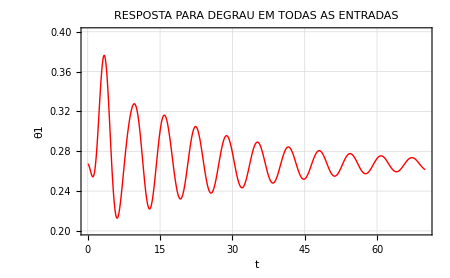

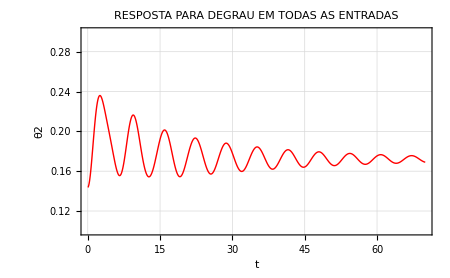

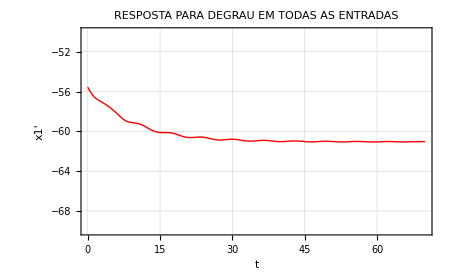

```mathematica
Entr={-6500,-2300,0};
GUdegrau[s]={(Entr[[1]] num11/den+Entr[[2]] num12/den+Entr[[3]] num13/den) 1/s,
(Entr[[1]] num21/den+Entr[[2]] num22/den+Entr[[3]] num23/den) 1/s,
(Entr[[1]] num31/den+Entr[[2]] num32/den+Entr[[3]] num33/den) 1/s};
Block[{response,plot},plot=(response=X0[[1]]+InverseLaplaceTransform[GUdegrau[s][[1]],s,t];
Plot[response,{t,0,70},PlotStyle->{Hue@(1),Thick},PlotRange-> {0.2,0.4},GridLines->Automatic,Frame->True,FrameLabel->{"t","θ1"},PlotLabel->StringForm["RESPOSTA PARA DEGRAU EM TODAS AS ENTRADAS"],ImageSize->{450,300}])]
Block[{response,plot},plot=(response=X0[[2]]+InverseLaplaceTransform[GUdegrau[s][[2]],s,t];
Plot[response,{t,0,70},PlotStyle->{Hue@(1),Thick},PlotRange-> {0.1,0.3},GridLines->Automatic,Frame->True,FrameLabel->{"t","θ2"},PlotLabel->StringForm["RESPOSTA PARA DEGRAU EM TODAS AS ENTRADAS"],ImageSize->{450,300}])]
Block[{response,plot},plot=(response=X0[[3]]+InverseLaplaceTransform[GUdegrau[s][[3]],s,t];
Plot[response,{t,0,70},PlotStyle->{Hue@(1),Thick},PlotRange-> {-70,-50},GridLines->Automatic,Frame->True,FrameLabel->{"t","x1'"},PlotLabel->StringForm["RESPOSTA PARA DEGRAU EM TODAS AS ENTRADAS"],ImageSize->{450,300}])]
```